```mathematica
(*--- Biophysical model of reverse blebbing: dynamics ---*)
(*--- Modified on 21/11/2021 ---*)
SetDirectory["/Users/cairola/Dropbox (The Francis Crick)/ChiuFanShared/Project-Glaucoma/paper"];
date=DateString[{"Year","_","Month","_","Day"}];
If[DirectoryQ[date]==False,CreateDirectory[date]];
SetDirectory[date];
SetOptions[Style,FontFamily->"Arial"];

(*--- Setting for figures ---*)
Size=20;imgSize=600;imagePadding={{110,80},{80,10}};
dashsty=Directive[Dashed,AbsoluteThickness[1]];
mdefault=Directive[Black,AbsoluteThickness[2]];
cdefault=Directive[Darker[RGBColor[0,154,0,255]],AbsoluteThickness[2]];
bfont=Directive[Size,Black,FontFamily->"Arial"];
rfont=Directive[Size,Darker[Red],FontFamily->"Arial"];
SetOptions[Plot,PlotRange->All];
SetOptions[ListPlot,PlotRange->All,Joined->True];
SetOptions[ListLogPlot,PlotRange->All,Joined->True];
```

```mathematica
(*--- Dynamical model ---*)
(*--- Generate inverse bleb dynamics ---*)
Clear[γM,ΤC,R0,P0,rm,αC,b,rE,ΔΑ,τ0,η0,cf];
(*--- Fixed parameters ---*)
(*--- 1. Membrane surface tension (pN/μm) ---*)
γM=40;
(*--- 2 Cell cortex surface tension (rest state) (pN/μm) ---*)
ΤC=374;
(*--- 3.1 Initial cell radius (μm) ---*)
(*--- Realistic values: 14-35 μm ---*)
R0=10.0;
(*--- 3.2 Initial intracellular pressure (pN/μm^2) ---*)
P0=2(γM+ΤC)/R0;
(*--- 4. Pore radius (μm) ---*)
(*--- Realistic values: 0.5-2 μm ---*)
rm=0.25;
(*--- 5. Reservoir size ---*)
(*--- Realistic values: 1%-30%  ---*)
αC=0.5;
(*--- 6. Membrane patch (μm) ---*)
(*--- Realistic values: 10 μm ---*)
rE=10.;
(*--- Thresholds ---*)
sC=(π rE^2)(1+αC);Δs=αC;
ΑC=(3π R0^2-π rE^2)(1+αC);ΔΑ=αC;
(*--- 7. Stretching strength ---*)
(*--- Realistic values: (1-2)10^5 pN/μm ---*)
b=1.0 10^5;
(*--- 8. Tension relaxation timescale (s) ---*)
τ0=1; τM=0.000001;
(*--- 9. Cytoplasmic viscosity (pN*s/μm) ---*)
ν0=2.5 10^4;
(*--- 10. Drag for lipid flow (pN*s/μm) ---*)
η0=1.7 10^3;
(*--- 11. Conversion factor Pa -> μm ---*)
cf=0.0075;
```

```mathematica
(*--- Generate trajectory ---*)
(*--- Initial conditions & simulation details ---*)
T=1500; dt=0.01;
σ0=γM+ΤC; Σ0=γM;
s0=π (rE)^2; Α0=3π (R0)^2-π (rE)^2;

(*--- Legend ---*)
(*--- Output vector ---*)
(*--- (Subscript[r, V],Subscript[r, C],Subscript[P, C],σ,Σ,ϕ) ---*)
Clear[sol,InflateGV,DeflateGV,σ,Σ,r,R,θ,Α,σL,λ,s,γ,Φ,s1,s2];

(*--- Dynamical equations ---*)
InflateGV[p_,t0_,rV0_,rC0_,a_,d_,ΓV0_,ΓC0_]:={
(*--- Initial conditions ---*)
r[t0]==rV0,σ[t0]==ΓC0,Σ[t0]==ΓV0,
(*--- Surface tensions ---*)
(*--- eq. 1: Cell ---*)
σ'[t]==1/λ[t](σL[t]-σ[t]),
(*--- eq. 2: Inverse bleb ---*)
(*--- cortex-dominated regime: pure growth term ---*)
(*--- membrane-dominated regime: lipid flow Φ ---*)
Σ'[t]==1/ξ[t](ΣL[t]-Σ[t]),
(*--- eq. 3: Inverse bleb radius ---*)
F[t]==(p-(2σ[t])/R[t]-(2Σ[t])/r[t]),
r'[t]==r[t]/(4ν0)F[t],
(*--- other specs: additional functions ---*)
(*--- eq 4: Cell radius ---*)
R[t]==((rC0)^3+2(r[t])^3(2+Cos[θ[t]])(Sin[θ[t]/2])^4)^(1/3),
(*--- eq 5: Inverse bleb opening angle ---*)
θ[t]==(π-ArcSin[a/r[t]]),
(*--- eq 6.1: Limit surface tension of the cell ---*)
Α[t]==3π (R[t])^2-π (d)^2,
σL[t]==(γM+ΤC)((1-s2[t])/2)+(γM+ΤC+b( Exp[(Α[t]-ΑC)/ΑC]-1))((1+s2[t])/2),
(*--- eq 6.2: Limit surface tension of the inverse bleb ---*)
s[t]==2π(r[t])^2(1-Cos[θ[t]])+π(d^2-a^2),
ΣL[t]==(γM+ΤC)((1-s1[t])/2)+(γM+ΤC+b( Exp[(s[t]-sC)/sC]-1))((1+s1[t])/2),
(*--- eq 7: Tensional timescales ---*)
ξ[t]==τ0((1-s1[t])/2)+τM((1+s1[t])/2),
λ[t]==τ0((1-s2[t])/2)+τM((1+s2[t])/2),
(*--- other specs: special events ---*)
(*--- 1. Inverse bleb area expansion ---*)
s1[t0]==-1,
WhenEvent[s[t]-sC>0,s1[t]->"DiscontinuitySignature"],
(*--- 2. Cell area expansion ---*)
s2[t0]==-1,
WhenEvent[Α[t]-ΑC>0,s2[t]->"DiscontinuitySignature"],
(*--- 2. Dealing with behaviour at hemisphere ---*)
WhenEvent[r[t]-a<10^-6,{ta=t,ra=r[t],σa=σ[t],Σa=Σ[t],"StopIntegration"},
"DetectionMethod"->"Interpolation","LocationMethod"->"BrentBracketRoot"]
};
DeflateGV[p_,t0_,rV0_,rC0_,a_,d_,ΓV0_,ΓC0_]:={
(*--- Initial conditions ---*)
r[t0]==rV0,σ[t0]==ΓC0,Σ[t0]==ΓV0,
(*--- Surface tensions ---*)
(*--- eq. 1: Cell ---*)
σ'[t]==1/λ[t](σL[t]-σ[t]),
(*--- eq. 2: Inverse bleb ---*)
(*--- cortex-dominated regime: pure growth term ---*)
(*--- membrane-dominated regime: lipid flow Φ ---*)
Σ'[t]==1/ξ[t](ΣL[t]-Σ[t]),
(*--- eq. 3: Inverse bleb radius ---*)
F[t]==(-p+(2σ[t])/R[t]+(2Σ[t])/r[t]),
r'[t]==r[t]/(4ν0)F[t],
(*--- other specs: additional functions ---*)
(*--- eq 4: Cell radius ---*)
R[t]==((rC0)^3+2(r[t])^3(2+Cos[θ[t]])(Sin[θ[t]/2])^4)^(1/3),
(*--- eq 5: Inverse bleb opening angle ---*)
θ[t]==(ArcSin[a/r[t]]),
(*--- eq 6.1: Limit surface tension of the cell ---*)
Α[t]==3π (R[t])^2-π (d)^2,
σL[t]==(γM+ΤC)((1-s2[t])/2)+(γM+ΤC+b( Exp[(Α[t]-ΑC)/ΑC]-1))((1+s2[t])/2),
(*--- eq 6.2: Limit surface tension of the inverse bleb ---*)
s[t]==2π(r[t])^2(1-Cos[θ[t]])+π(d^2-a^2),
ΣL[t]==(γM+ΤC)((1-s1[t])/2)+(γM+ΤC+b( Exp[(s[t]-sC)/sC]-1))((1+s1[t])/2),
(*--- eq 7: Tensional timescales ---*)
ξ[t]==τ0((1-s1[t])/2)+τM((1+s1[t])/2),
λ[t]==τ0((1-s2[t])/2)+τM((1+s2[t])/2),
(*--- other specs: special events ---*)
(*--- 1. Inverse bleb area expansion ---*)
s1[t0]==-1,
WhenEvent[s[t]-sC>0,s1[t]->"DiscontinuitySignature"],
(*--- 2. Cell area expansion ---*)
s2[t0]==-1,
WhenEvent[Α[t]-ΑC>0,s2[t]->"DiscontinuitySignature"],
(*--- 2. Dealing with behaviour at hemisphere ---*)
WhenEvent[r[t]-a<10^-6,{ta=t,ra=r[t],σa=σ[t],Σa=Σ[t],"StopIntegration"},
"DetectionMethod"->"Interpolation","LocationMethod"->"BrentBracketRoot"]
};


vars={r[t],R[t],θ[t],σ[t],Σ[t],F[t],s1[t],s2[t]};
(*--- Case 1: Vacuole inflation ---*)
Δp=30.0/cf;r0=rm 1.0000001;
sol=NDSolve[InflateGV[Δp,0,r0,R0,rm,rE,Σ0,σ0],vars,{t,0,T},DiscreteVariables->{s1[t]∈{-1,1},s2[t]∈{-1,1}}];
(*--- Case 2: Vacuole deflation ---*)
Δp=1.0/cf;r0=rm 1.0000001;
sol2=NDSolve[DeflateGV[Δp,0,r0,R0,rm,rE,Σ0,σ0],vars,{t,0,T},DiscreteVariables->{s1[t]∈{-1,1},s2[t]∈{-1,1}}]; (*Print[ta]; Print[ra];*)

r1[t_]:=Evaluate[{r[t]}]/.sol;
R1[t_]:=Evaluate[{R[t]}]/.sol;
ϕ1[t_]:=Evaluate[{θ[t]}]/.sol;
V1[t_]:=4/3 π r1[t]^3(2+Cos[ϕ1[t]])(Sin[ϕ1[t]/2])^4;
y1[t_]:=Evaluate[{σ[t]}]/.sol;
z1[t_]:=Evaluate[{Σ[t]}]/.sol;
P1[t_]:=(2y1[t])/R1[t];
force[t]:=Evaluate[{F[t]}]/.sol;
(*(*--- Integration beyond switch point ---*)
sol2=NDSolve[EqsSet[Δp,ta,ra,R0,rm,Σ0,σ0,0],vars,{t,ta,T},DiscreteVariables->{(*s1[t]∈{-1,1},*)s2[t]∈{-1,1}}];
x2[t_]:=Evaluate[{r[t]}]/.sol2;
ϕ2[t_]:=Evaluate[{θ[t]}]/.sol2;
V2[t_]:=4/3 π x2[t]^3(2+Cos[ϕ2[t]])(Sin[ϕ2[t]/2])^4;
y2[t_]:=Evaluate[{σ[t]}]/.sol2;
z2[t_]:=Evaluate[{Σ[t]}]/.sol2;*)
```

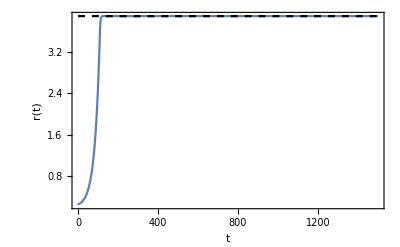

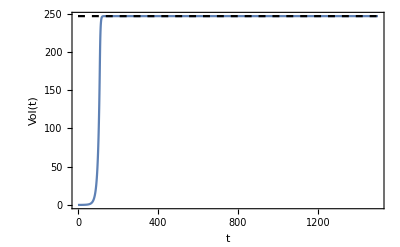

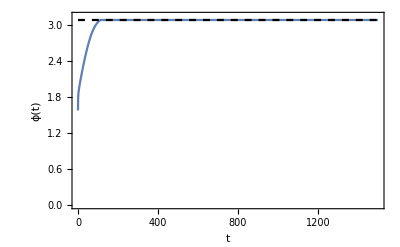

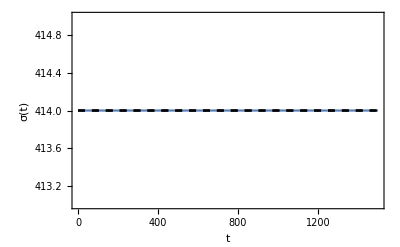

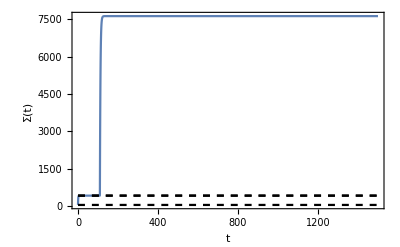

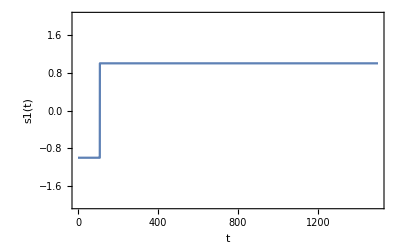

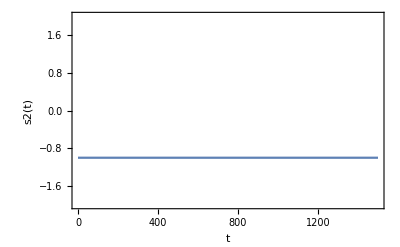

```mathematica
(*--- 2.1 Plot numerical results ---*)
areaV[r_,ϕ_]:=2π r^2(1-Cos[ϕ]);
VacV[x_,ϕ_]:=Module[{z},
z=4/3 π x^3(2+Cos[ϕ])(Sin[ϕ/2])^4;
Return[z];
]
(*--- Stationary solution: 30 mmHg ---*)
rVst=3.8914346609433457; rCst=10.37836251413144;Pst=79.78137195271164; σst=414;Σst=7627.637323829492; ϕst=3.0773047210846802;
Vst=VacV[rVst,ϕst];
(*--- Stationary solution: 8 mmHg ---*)
(*rVst=3.35635961959729; rCst=8.192267525260545;Pst=310.0036811877257; σst=1269.8165450527144;Σst=1269.8165450527144; ϕst=3.0670381428708535;
Vst=VacV[rVst,ϕst];*)
(*--- Stationary solution: 1 mmHg ---*)
(*rVst=27.759743286745096; rCst=8.000000137422031; Pst=103.50463259751679; σst=414.0185375019756; Σst=414.0185375019756; ϕst=0.009005968712591475;
Vst=VacV[rVst,ϕst];*)

(*--- a. r(t) ---*)
Show[Plot[r1[t],{t,0,T}],
Plot[rVst,{t,0,T},PlotStyle->{Dashed,Black}],
PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},
FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["r(t)",bfont]}
]
(*--- b. vol(t) ---*)
Show[Plot[V1[t],{t,0,T}],
Plot[Vst,{t,0,T},PlotStyle->{Dashed,Black}],
PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},
FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["Vol(t)",bfont]}
]
(*--- b. ϕ(t) ---*)
Show[Plot[ϕ1[t],{t,0,T},PlotRange->{All,{0,π}}],
Plot[ϕst,{t,0,T},PlotStyle->{Dashed,Black}],
Axes->False,Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["ϕ(t)",bfont]}
]
(*--- a. σ(t) ---*)
Show[Plot[y1[t],{t,0,T},PlotRange->All],
Plot[σst,{t,0,T},PlotStyle->{Dashed,Black}],
Plot[σ0,{t,0,T},PlotStyle->{Dashed,Black}],
Axes->False,Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["σ(t)",bfont]}
]
(*--- a. Σ(t) ---*)
Show[Plot[z1[t],{t,0,T},PlotRange->All],
Plot[σst,{t,0,T},PlotStyle->{Dashed,Black}],
Plot[γM,{t,0,T},PlotStyle->{Dashed,Black}],
Plot[σ0,{t,0,T},PlotStyle->{Dashed,Black}],
Axes->False,Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["Σ(t)",bfont]}
]

Plot[Evaluate[{s1[t]}]/.sol,{t,0,T},PlotRange->{All,{-2,2}},Axes->False,
Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["s1(t)",bfont]}]
Plot[Evaluate[{s2[t]}]/.sol,{t,0,T},PlotRange->{All,{-2,2}},Axes->False,
Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["s2(t)",bfont]}]
```

```mathematica
(*--- Vacuole inflation: Membrane dominated phase ---*)

(*--- Generate discrete data ---*)
linspace[a_,b_,d_]:=Range[a,b,d];
t1=0;t2=5 60;Δt=0.05;
ρ=linspace[t1,t2,Δt];

indx=1; dat1=Table[{ρ[[i]],Flatten[(Evaluate[{r[t],R[t],(2σ[t])/R[t],Σ[t],σ[t],θ[t]}]/.sol)/.t->ρ[[i]]],First[Flatten[(Evaluate[F[t]]/.sol)/.t->ρ[[i]]]],1},{i,1,Length[ρ]}];Export[StringJoin["dat_",ToString[indx],".txt"],dat1,"Table"];

t1=0;t2=5 60;tconv=60;
t1=t1/tconv; t2=t2/tconv;
```

```mathematica
(*--- Equilibrium solutions ---*)
(*--- Index 1 ---*)
(*Subscript[T, 0]=374 pN/μm*)
eqsol1={{3.8914346609433457,10.37836251413144,79.78137195271164 ,7627.637323829492,414,3.0773047210846802}};

(*--- Manage data ---*)
tab1=Table[{dat1[[n,1]]/tconv,dat1[[n,2]]},{n,1,Length[dat1]}];
F1=Table[{dat1[[n,1]]/tconv,dat1[[n,3]]},{n,1,Length[dat1]}];
flag1=Table[{dat1[[n,1]]/tconv,dat1[[n,4]]},{n,1,Length[dat1]}];
Table[If[flag1[[n,2]]==0,F1[[n,2]]*=(-1)],{n,1,Length[dat1]}];
```

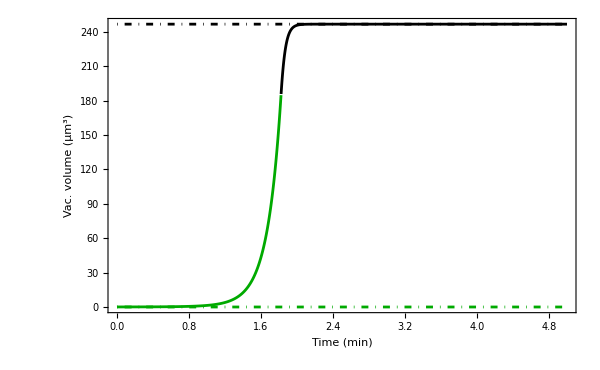

```mathematica
(*--- A. Membrane dominated phase ---*)
(*--- Index 1, 4 ---*)
(*indx=1;t1=0;t2=20;*)
(*--- Index 2, 3 ---*)
(*t1=24.6;t2=40;*)
rVdat1=Table[{tab1[[n,1]],tab1[[n,2,1]]},{n,1,Length[tab1]}];
rCdat1=Table[{tab1[[n,1]],tab1[[n,2,2]]},{n,1,Length[tab1]}];
PCdat1=Table[{tab1[[n,1]],tab1[[n,2,3]]cf},{n,1,Length[tab1]}];
ΓVdat1=Table[{tab1[[n,1]],tab1[[n,2,4]]},{n,1,Length[tab1]}];
ΓCdat1=Table[{tab1[[n,1]],tab1[[n,2,5]]},{n,1,Length[tab1]}];
ϕdat1=Table[{tab1[[n,1]],tab1[[n,2,6]]},{n,1,Length[tab1]}];
(*F1=Table[If[flag1[[n,2]]==0,F1[[n,2]]*=(-1)],{n,1,Length[tab1]}];*)

(*--- A.1 Vacuole volume and area ---*)
vacV[x_,ϕ_]:=Module[{z},
z=4/3 π x^3(2+Cos[ϕ])(Sin[ϕ/2])^4;
Return[z];
]
Av[x_,ϕ_]:=Module[{z},z=2π x^2(1-Cos[ϕ])+π(rE^2-rm^2);Return[z];]

ΑVdat1=Table[{tab1[[n,1]],Av[rVdat1[[n,2]],ϕdat1[[n,2]]]},{n,1,Length[tab1]}];
Α1dat1=Table[If[ΑVdat1[[n,2]]≤sC,{ΑVdat1[[n,1]],vacV[rVdat1[[n,2]],ϕdat1[[n,2]]]}],{n,1,Length[tab1]}];
Α1dat1=Select[Α1dat1,Length[#]==2&];
Α2dat1=Table[If[ΑVdat1[[n,2]]>sC,{ΑVdat1[[n,1]],vacV[rVdat1[[n,2]],ϕdat1[[n,2]]]}],{n,1,Length[tab1]}];
Α2dat1=Select[Α2dat1,Length[#]==2&];
(*DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΑVdat1,Α1dat1];*)

f11=Show[Plot[vacV[eqsol1[[1,1]],eqsol1[[1,6]]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α1dat1,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat1,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},All},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vac. volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name11=StringJoin["volumeV_",ToString[indx],".pdf"];
Export[name11,f11];
```

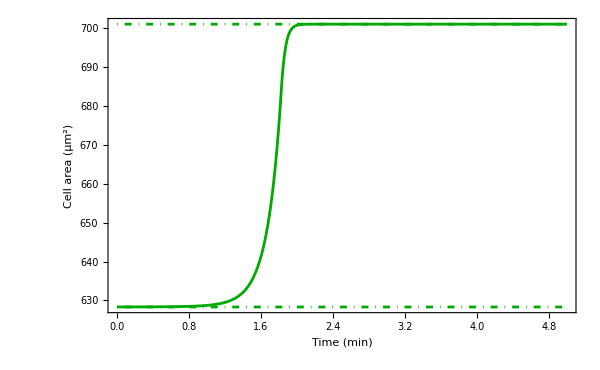

```mathematica
(*--- A.1 Cell area ---*)
ΑCdat1=Table[{tab1[[n,1]],3π (rCdat1[[n,2]])^2-π rE^2},{n,1,Length[tab1]}];
Α3dat1=Table[If[ΑCdat1[[n,2]]≤ΑC,ΑCdat1[[n]]],{n,1,Length[tab1]}];
Α3dat1=Select[Α3dat1,Length[#]==2&];
Α4dat1=Table[If[ΑCdat1[[n,2]]>ΑC,ΑCdat1[[n]]],{n,1,Length[tab1]}];
Α4dat1=Select[Α4dat1,Length[#]==2&];

f11=Show[Plot[3π (eqsol1[[1,2]])^2-π rE^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[3π R0^2-π rE^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α3dat1,Joined->True,PlotStyle->cdefault],
ListPlot[Α4dat1,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},{3π R0^2-π rE^2,Max[Α3dat1[[;;,2]]]}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Cell area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name11=StringJoin["cellA_",ToString[indx],".pdf"];
Export[name11,f11];
```

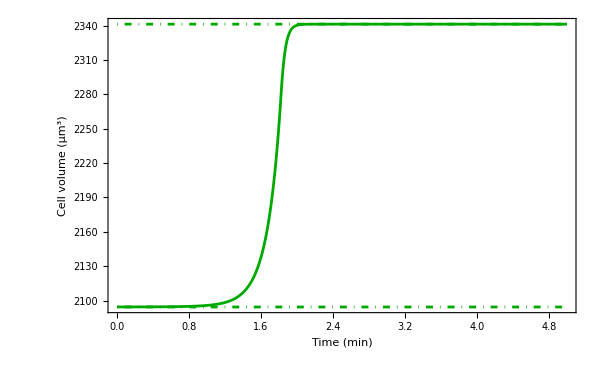

```mathematica
(*--- A.1 Cell volume ---*)
volCdat1=Table[{tab1[[n,1]],2π (rCdat1[[n,2]])^3/3},{n,1,Length[tab1]}];
vol3dat1=Table[If[ΑCdat1[[n,2]]≤ΑC,volCdat1[[n]]],{n,1,Length[tab1]}];
vol3dat1=Select[vol3dat1,Length[#]==2&];
vol4dat1=Table[If[ΑCdat1[[n,2]]>ΑC,volCdat1[[n]]],{n,1,Length[tab1]}];
vol4dat1=Select[vol4dat1,Length[#]==2&];

f18=Show[Plot[2π (eqsol1[[1,2]])^3/3,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[2π R0^3/3,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[vol3dat1,Joined->True,PlotStyle->cdefault],
ListPlot[vol4dat1,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},{2π R0^3/3,Max[vol3dat1[[;;,2]]]}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Cell volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name18=StringJoin["cellV_",ToString[indx],".pdf"];
Export[name18,f18];
```

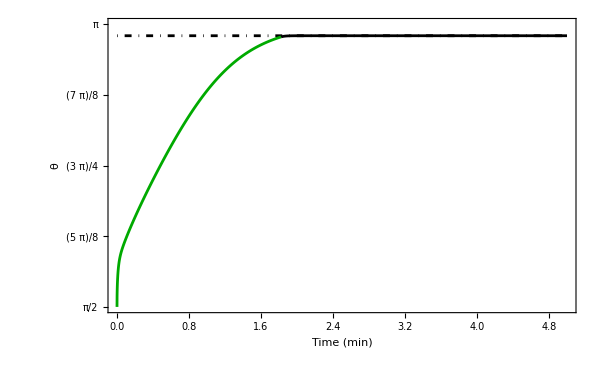

```mathematica
(*--- A.2 Vacuole geometry ---*)
ϕ1dat1=Table[If[ΑVdat1[[n,2]]≤sC,ϕdat1[[n]]],{n,1,Length[tab1]}];
ϕ1dat1=Select[ϕ1dat1,Length[#]==2&];
ϕ2dat1=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ϕdat1,ϕ1dat1];

f12=Show[Plot[eqsol1[[1,6]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
ListPlot[ϕ1dat1,Joined->True,PlotStyle->cdefault],
ListPlot[ϕ2dat1,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},{Pi/2,Pi}},Frame->True,BaseStyle->bfont,
FrameTicks->{{{π/2,5π/8,3π/4,7π/8,π},{π/2,5π/8,3π/4,7π/8,π}},{Automatic,Automatic}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}},
FrameLabel->{Style["Time (min)",bfont],Style["θ",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name12=StringJoin["phi_",ToString[indx],".pdf"];
Export[name12,f12];
```

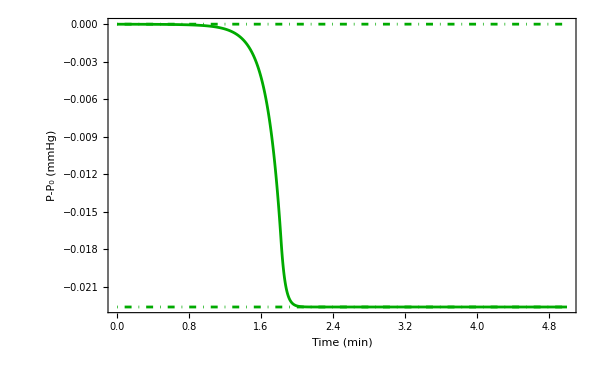

```mathematica
(*--- A.3 Intracellular pressure ---*)
PC1dat1=Table[If[ΑCdat1[[n,2]]≤ΑC,{PCdat1[[n,1]],PCdat1[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab1]}];
PC1dat1=Select[PC1dat1,Length[#]==2&];
PC2dat1=Table[If[ΑCdat1[[n,2]]>ΑC,{PCdat1[[n,1]],PCdat1[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab1]}];
PC2dat1=Select[PC2dat1,Length[#]==2&];

f13=Show[Plot[eqsol1[[1,3]]cf-(2(γM+ΤC)/R0) cf,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[0,{x,t1,t2},PlotRange->All,PlotStyle->{cdefault,DotDashed}],
ListPlot[PC1dat1,Joined->True,PlotStyle->cdefault],
ListPlot[PC2dat1,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},
Frame->True,BaseStyle->bfont,FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["P-P_0 (mmHg)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name13=StringJoin["press_",ToString[indx],".pdf"];
Export[name13,f13];
```

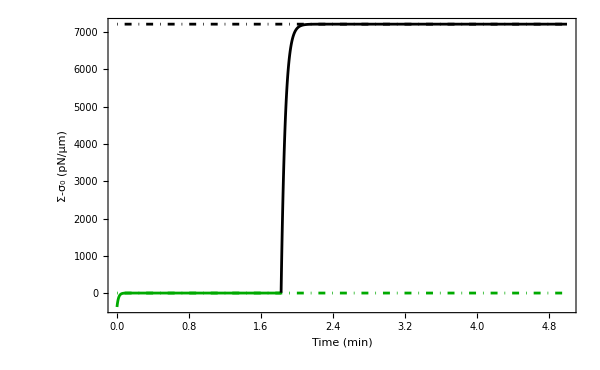

```mathematica
(*--- A.4.1 Vacuole surface tension ---*)
ΓV1dat1=Table[If[ΑVdat1[[n,2]]≤sC,ΓVdat1[[n]]],{n,1,Length[tab1]}];
ΓV1dat1=Select[ΓV1dat1,Length[#]==2&];
ΓV2dat1=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΓVdat1,ΓV1dat1];

ΓV1dat1=ParallelTable[{ΓV1dat1[[n,1]],ΓV1dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓV1dat1]}];
ΓV2dat1=ParallelTable[{ΓV2dat1[[n,1]],ΓV2dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓV2dat1]}];

f14=Show[Plot[eqsol1[[1,4]]-(γM+ΤC),{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[0,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓV1dat1,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓV2dat1,Joined->True,PlotStyle->{mdefault,Dashed}],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,Axes->False,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name14=StringJoin["tensionV_",ToString[indx],".pdf"];
Export[name14,f14];
```

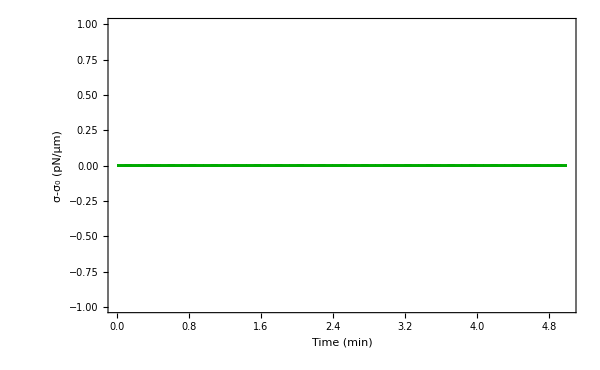

```mathematica
(*--- A.4.2 Cell surface tension ---*)
ΓC1dat1=Table[If[ΑCdat1[[n,2]]-π rm^2≤ΑC,ΓCdat1[[n]]],{n,1,Length[tab1]}];
ΓC1dat1=Select[ΓC1dat1,Length[#]==2&];
ΓC2dat1=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΓCdat1,ΓC1dat1];

ΓC1dat1=ParallelTable[{ΓC1dat1[[n,1]],ΓC1dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓC1dat1]}];
ΓC2dat1=ParallelTable[{ΓC2dat1[[n,1]],ΓC2dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓC2dat1]}];

f16=Show[Plot[eqsol1[[1,5]]-(γM+ΤC),{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[0,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓC1dat1,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓC2dat1,Joined->True,PlotStyle->{mdefault,Dashed}],ListPlot[ΓC1dat1,Joined->True,PlotStyle->{cdefault}],
PlotRange->{{t1,t2},{-1,1}},Frame->True,BaseStyle->bfont,Axes->False,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name16=StringJoin["tensionC_",ToString[indx],".pdf"];
Export[name16,f16];
```

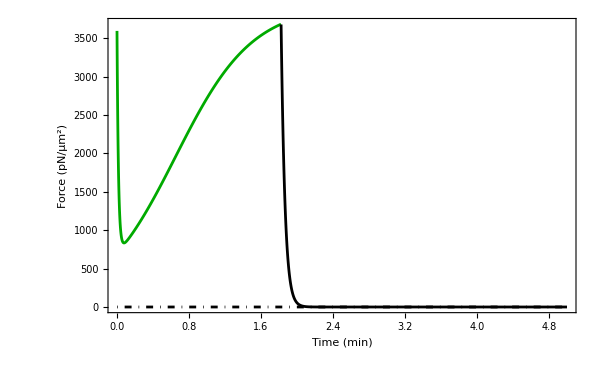

```mathematica
(*--- A.5 Force on vacuole ---*)
F11=Table[If[ΑVdat1[[n,2]]≤sC,F1[[n]]],{n,1,Length[tab1]}];
F11=Select[F11,Length[#]==2&];
F12=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[F1,F11];

f15=Show[Plot[0,{x,t1,t2},PlotStyle->{DotDashed,mdefault}],
ListPlot[F11,Joined->True,PlotStyle->cdefault],
ListPlot[F12,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicksStyle->{Directive[bfont,FontFamily->"Arial"],bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Force (pN/μm^2)",bfont]},FrameStyle->{{bfont,bfont},{bfont,bfont}},ImageSize->imgSize,ImagePadding->imagePadding]
name15=StringJoin["force_",ToString[indx],".pdf"];
Export[name15,f15];
```

```mathematica
(*--- Vacuole deflation: Low pressure ---*)

(*--- Generate discrete data ---*)
linspace[a_,b_,d_]:=Range[a,b,d];
t1=0;t2=15 60;Δt=0.05;
ρ=linspace[t1,t2,Δt];
indx=2; dat2=Table[{ρ[[i]],Flatten[(Evaluate[{r[t],R[t],(2σ[t])/R[t],Σ[t],σ[t],θ[t]}]/.sol2)/.t->ρ[[i]]],First[Flatten[(Evaluate[F[t]]/.sol2)/.t->ρ[[i]]]],0},{i,1,Length[ρ]}];Export[StringJoin["dat_",ToString[indx],".txt"],dat2,"Table"];

t1=0;t2=15 60;tconv=60;
t1=t1/tconv; t2=t2/tconv;
```

```mathematica
(*--- Stationary solution: 1 mmHg ---*)
eqsol1={{27.759743286745096,8.000000137422031,103.50463259751679,414.0185375019756,414.0185375019756,0.009005968712591475}};
Vst=VacV[rVst,ϕst];

tab1=Table[{dat2[[n,1]]/tconv,dat2[[n,2]]},{n,1,Length[ρ]}];
F2=Table[{dat2[[n,1]]/tconv,dat2[[n,3]]},{n,1,Length[ρ]}];
flag2=Table[{dat2[[n,1]]/tconv,dat2[[n,4]]},{n,1,Length[ρ]}];
Table[If[flag2[[n,2]]==0,F2[[n,2]]*=(-1)],{n,1,Length[ρ]}];
```

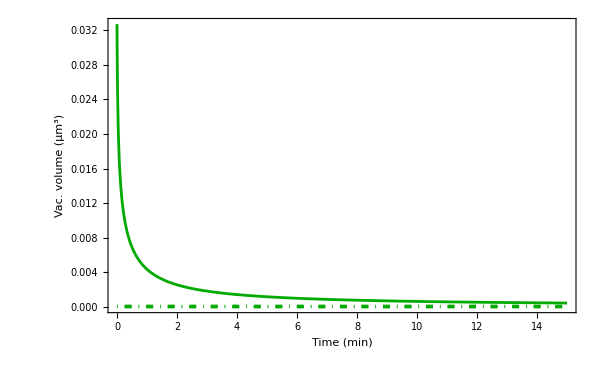

```mathematica
(*--- Plots ---*)
rVdat1=Table[{tab1[[n,1]],tab1[[n,2,1]]},{n,1,Length[tab1]}];
rCdat1=Table[{tab1[[n,1]],tab1[[n,2,2]]},{n,1,Length[tab1]}];
PCdat1=Table[{tab1[[n,1]],tab1[[n,2,3]]cf},{n,1,Length[tab1]}];
ΓVdat1=Table[{tab1[[n,1]],tab1[[n,2,4]]},{n,1,Length[tab1]}];
ΓCdat1=Table[{tab1[[n,1]],tab1[[n,2,5]]},{n,1,Length[tab1]}];
ϕdat1=Table[{tab1[[n,1]],tab1[[n,2,6]]},{n,1,Length[tab1]}];
(*F1=Table[If[flag1[[n,2]]==0,F1[[n,2]]*=(-1)],{n,1,Length[tab1]}];*)

(*--- A.1 Vacuole volume and area ---*)
vacV[x_,ϕ_]:=Module[{z},
z=4/3 π x^3(2+Cos[ϕ])(Sin[ϕ/2])^4;
Return[z];
]
Av[x_,ϕ_]:=Module[{z},z=2π x^2(1-Cos[ϕ]);Return[z];]

ΑVdat1=Table[{tab1[[n,1]],Av[rVdat1[[n,2]],ϕdat1[[n,2]]]},{n,1,Length[tab1]}];
Α1dat1=Table[If[ΑVdat1[[n,2]]≤sC,{ΑVdat1[[n,1]],vacV[rVdat1[[n,2]],ϕdat1[[n,2]]]}],{n,1,Length[tab1]}];
Α1dat1=Select[Α1dat1,Length[#]==2&];
Α2dat1=Table[If[ΑVdat1[[n,2]]>sC,{ΑVdat1[[n,1]],vacV[rVdat1[[n,2]],ϕdat1[[n,2]]]}],{n,1,Length[tab1]}];
Α2dat1=Select[Α2dat1,Length[#]==2&];
(*DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΑVdat1,Α1dat1];*)

f11=Show[Plot[vacV[eqsol1[[1,1]],eqsol1[[1,6]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α1dat1,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat1,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},All},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vac. volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name11=StringJoin["volumeV_",ToString[indx],".pdf"];
Export[name11,f11];
```

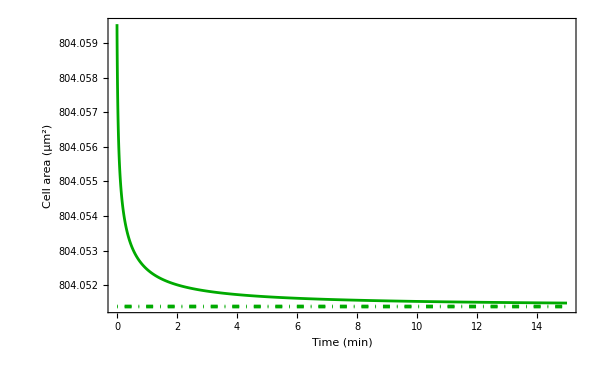

```mathematica
(*--- A.1 Cell area ---*)
ΑCdat1=Table[{tab1[[n,1]],4π (rCdat1[[n,2]])^2-π rm^2},{n,1,Length[tab1]}];
Α3dat1=Table[If[ΑCdat1[[n,2]]≤ΑC,ΑCdat1[[n]]],{n,1,Length[tab1]}];
Α3dat1=Select[Α3dat1,Length[#]==2&];
Α4dat1=Table[If[ΑCdat1[[n,2]]>ΑC,ΑCdat1[[n]]],{n,1,Length[tab1]}];
Α4dat1=Select[Α4dat1,Length[#]==2&];

f11=Show[Plot[4π (eqsol1[[1,2]])^2-π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[4π R0^2-π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α3dat1,Joined->True,PlotStyle->cdefault],
ListPlot[Α4dat1,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},{4π R0^2-π rm^2,Max[Α3dat1[[;;,2]]]}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Cell area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name11=StringJoin["cellA_",ToString[indx],".pdf"];
Export[name11,f11];
```

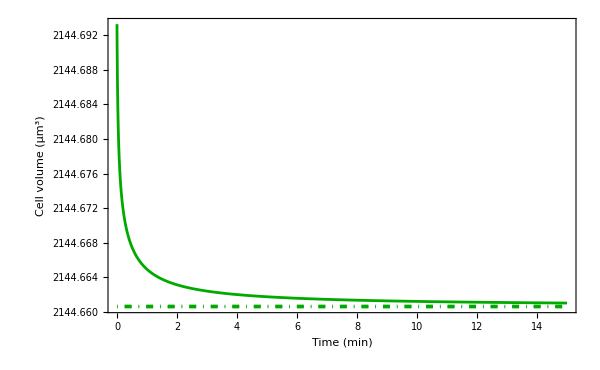

```mathematica
(*--- A.1 Cell volume ---*)
volCdat1=Table[{tab1[[n,1]],4π (rCdat1[[n,2]])^3/3},{n,1,Length[tab1]}];
vol3dat1=Table[If[ΑCdat1[[n,2]]≤ΑC,volCdat1[[n]]],{n,1,Length[tab1]}];
vol3dat1=Select[vol3dat1,Length[#]==2&];
vol4dat1=Table[If[ΑCdat1[[n,2]]>ΑC,volCdat1[[n]]],{n,1,Length[tab1]}];
vol4dat1=Select[vol4dat1,Length[#]==2&];

f18=Show[Plot[4π (eqsol1[[1,2]])^3/3,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[4π R0^3/3,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[vol3dat1,Joined->True,PlotStyle->cdefault],
ListPlot[vol4dat1,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},{4π R0^3/3,Max[vol3dat1[[;;,2]]]}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Cell volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name18=StringJoin["cellV_",ToString[indx],".pdf"];
Export[name18,f18];
```

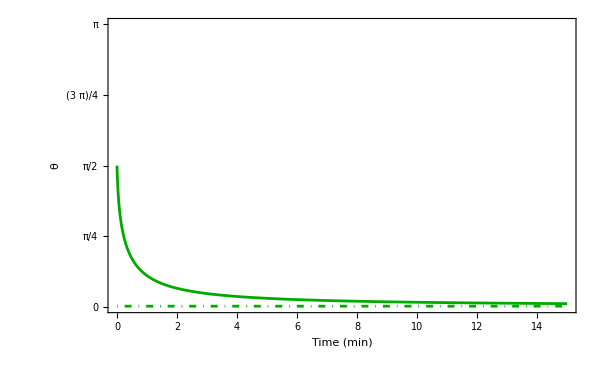

```mathematica
(*--- A.2 Vacuole geometry ---*)
ϕ1dat1=Table[If[ΑVdat1[[n,2]]≤sC,ϕdat1[[n]]],{n,1,Length[tab1]}];
ϕ1dat1=Select[ϕ1dat1,Length[#]==2&];
ϕ2dat1=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ϕdat1,ϕ1dat1];

f12=Show[Plot[eqsol1[[1,6]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ϕ1dat1,Joined->True,PlotStyle->cdefault],
ListPlot[ϕ2dat1,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},{0,Pi}},Frame->True,BaseStyle->bfont,
FrameTicks->{{{0,π/4,π/2,3π/4,π},{0,π/4,π/2,3π/4,π}},{Automatic,Automatic}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}},
FrameLabel->{Style["Time (min)",bfont],Style["θ",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name12=StringJoin["phi_",ToString[indx],".pdf"];
Export[name12,f12];
```

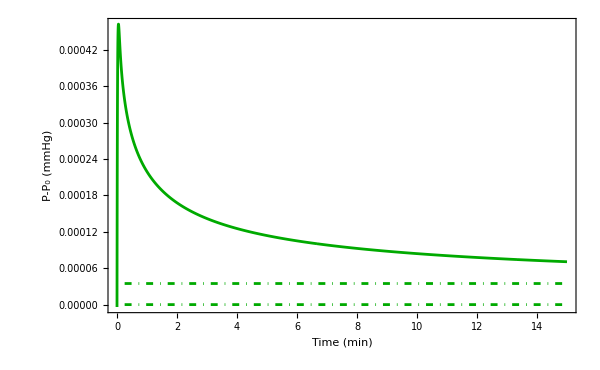

```mathematica
(*--- A.3 Intracellular pressure ---*)
PC1dat1=Table[If[ΑCdat1[[n,2]]≤ΑC,{PCdat1[[n,1]],PCdat1[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab1]}];
PC1dat1=Select[PC1dat1,Length[#]==2&];
PC2dat1=Table[If[ΑCdat1[[n,2]]>ΑC,{PCdat1[[n,1]],PCdat1[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab1]}];
PC2dat1=Select[PC2dat1,Length[#]==2&];

f13=Show[Plot[eqsol1[[1,3]]cf-(2(γM+ΤC)/R0) cf,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[0,{x,t1,t2},PlotRange->All,PlotStyle->{cdefault,DotDashed}],
ListPlot[PC1dat1,Joined->True,PlotStyle->cdefault],
ListPlot[PC2dat1,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},
Frame->True,BaseStyle->bfont,FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["P-P_0 (mmHg)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name13=StringJoin["press_",ToString[indx],".pdf"];
Export[name13,f13];
```

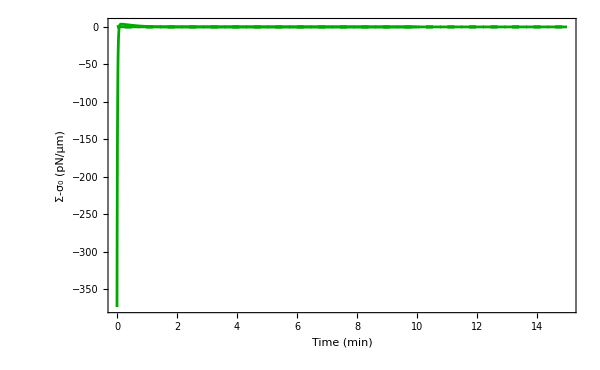

```mathematica
(*--- A.4.1 Vacuole surface tension ---*)
ΓV1dat1=Table[If[ΑVdat1[[n,2]]≤sC,ΓVdat1[[n]]],{n,1,Length[tab1]}];
ΓV1dat1=Select[ΓV1dat1,Length[#]==2&];
ΓV2dat1=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΓVdat1,ΓV1dat1];

ΓV1dat1=ParallelTable[{ΓV1dat1[[n,1]],ΓV1dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓV1dat1]}];
ΓV2dat1=ParallelTable[{ΓV2dat1[[n,1]],ΓV2dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓV2dat1]}];

f14=Show[Plot[eqsol1[[1,4]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[0,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓV1dat1,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓV2dat1,Joined->True,PlotStyle->{mdefault,Dashed}],ListPlot[ΓC1dat1,Joined->True,PlotStyle->{cdefault}],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,Axes->False,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name14=StringJoin["tensionV_",ToString[indx],".pdf"];
Export[name14,f14];
```

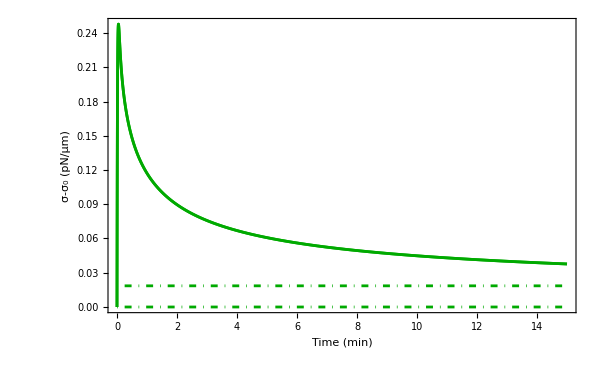

```mathematica
(*--- A.4.2 Cell surface tension ---*)
ΓC1dat1=Table[If[ΑCdat1[[n,2]]-π rm^2≤ΑC,ΓCdat1[[n]]],{n,1,Length[tab1]}];
ΓC1dat1=Select[ΓC1dat1,Length[#]==2&];
ΓC2dat1=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΓCdat1,ΓC1dat1];

ΓC1dat1=ParallelTable[{ΓC1dat1[[n,1]],ΓC1dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓC1dat1]}];
ΓC2dat1=ParallelTable[{ΓC2dat1[[n,1]],ΓC2dat1[[n,2]]-(γM+ΤC)},{n,1,Length[ΓC2dat1]}];

f16=Show[Plot[eqsol1[[1,4]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[0,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓC1dat1,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓC2dat1,Joined->True,PlotStyle->{mdefault,Dashed}],ListPlot[ΓC1dat1,Joined->True,PlotStyle->{cdefault}],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,Axes->False,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name16=StringJoin["tensionC_",ToString[indx],".pdf"];
Export[name16,f16];
```

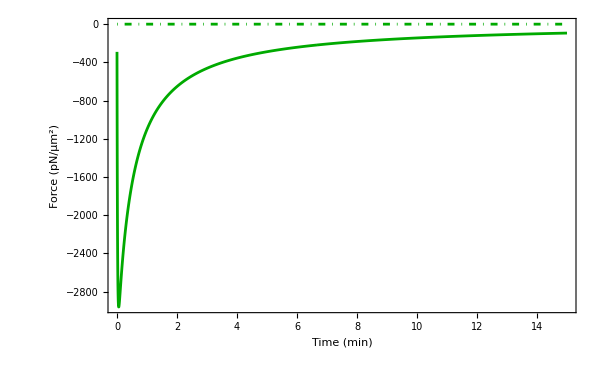

```mathematica
(*--- A.5 Force on vacuole ---*)
F11=Table[If[ΑVdat1[[n,2]]≤sC,F2[[n]]],{n,1,Length[tab1]}];
F11=Select[F11,Length[#]==2&];
F12=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[F2,F11];

f15=Show[Plot[0,{x,t1,t2},PlotStyle->{DotDashed,cdefault}],
ListPlot[F11,Joined->True,PlotStyle->cdefault],
ListPlot[F12,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicksStyle->{Directive[bfont,FontFamily->"Arial"],bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Force (pN/μm^2)",bfont]},FrameStyle->{{bfont,bfont},{bfont,bfont}},ImageSize->imgSize,ImagePadding->imagePadding]
name15=StringJoin["force_",ToString[indx],".pdf"];
Export[name15,f15];
```

```mathematica
(*--- B. Metastability ---*)
Δp=8.0/cf;r0=0.85;
sol1=NDSolve[InflateGV[Δp,0,r0,R0,rm,Σ0,σ0],vars,{t,0,T},DiscreteVariables->{s1[t]∈{-1,1},s2[t]∈{-1,1}}]; 
sol2=NDSolve[DeflateGV[Δp,ta,ra,R0,rm,Σa,σa],vars,{t,0,T},DiscreteVariables->{s1[t]∈{-1,1},s2[t]∈{-1,1}}];
Δp=8.0/cf;r0=0.867;
sol3=NDSolve[InflateGV[Δp,0,r0,R0,rm,Σ0,σ0],vars,{t,0,T},DiscreteVariables->{s1[t]∈{-1,1},s2[t]∈{-1,1}}];
```

```mathematica
(*--- Generate discrete data ---*)
linspace[a_,b_,d_]:=Range[a,b,d];
t1=0;t2=20 60;Δt=0.05;
ρ=linspace[t1,t2,Δt];
(*--- Deflating solution ---*)
indx=3; dat3=Table[If[ρ[[i]]≤ta,
{ρ[[i]],Flatten[(Evaluate[{r[t],R[t],(2σ[t])/R[t],Σ[t],σ[t],θ[t]}]/.sol1)/.t->ρ[[i]]],First[Flatten[(Evaluate[F[t]]/.sol1)/.t->ρ[[i]]]],1},
{ρ[[i]],Flatten[(Evaluate[{r[t],R[t],(2σ[t])/R[t],Σ[t],σ[t],θ[t]}]/.sol2)/.t->ρ[[i]]],First[Flatten[(Evaluate[F[t]]/.sol2)/.t->ρ[[i]]]],0}]
,{i,1,Length[ρ]}];
Export[StringJoin["dat_",ToString[indx],".txt"],dat3,"Table"];
(*--- Inflating solution ---*)
indx=4; dat4=Table[
{ρ[[i]],Flatten[(Evaluate[{r[t],R[t],(2σ[t])/R[t],Σ[t],σ[t],θ[t]}]/.sol3)/.t->ρ[[i]]],First[Flatten[(Evaluate[F[t]]/.sol3)/.t->ρ[[i]]]],1}
,{i,1,Length[ρ]}];
Export[StringJoin["dat_",ToString[indx],".txt"],dat4,"Table"];

t1=0;t2=20 60;tconv=60;
t1=t1/tconv; t2=t2/tconv;
```

```mathematica
(*--- Stationary solution: 1 mmHg ---*)
eqsol3={{0.8599100181968837,8.00000456744084,103.52665862380007,414.1068709211446,414.1068709211446,0.2949877124003864},{0.8663163421960165,8.003380362105094,104.18290453618152,416.9077061159725,416.9077061159725,2.848851138051944},{3.35635961959729,8.192267525260545,310.0036811877257,1269.8165450527144,1269.8165450527144,3.0670381428708535}};

tab2=Table[{dat3[[n,1]]/tconv,dat3[[n,2]]},{n,1,Length[ρ]}];
F2=Table[{dat3[[n,1]]/tconv,dat3[[n,3]]},{n,1,Length[ρ]}];
flag2=Table[{dat3[[n,1]]/tconv,dat3[[n,4]]},{n,1,Length[ρ]}];
Table[If[flag2[[n,2]]==0,F2[[n,2]]*=(-1)],{n,1,Length[ρ]}];

tab4=Table[{dat4[[n,1]]/tconv,dat4[[n,2]]},{n,1,Length[ρ]}];
F4=Table[{dat4[[n,1]]/tconv,dat4[[n,3]]},{n,1,Length[ρ]}];
flag4=Table[{dat4[[n,1]]/tconv,dat4[[n,4]]},{n,1,Length[ρ]}];
Table[If[flag4[[n,2]]==0,F4[[n,2]]*=(-1)],{n,1,Length[ρ]}];
```

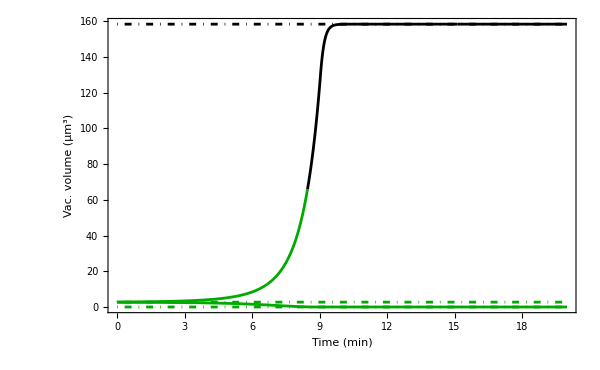

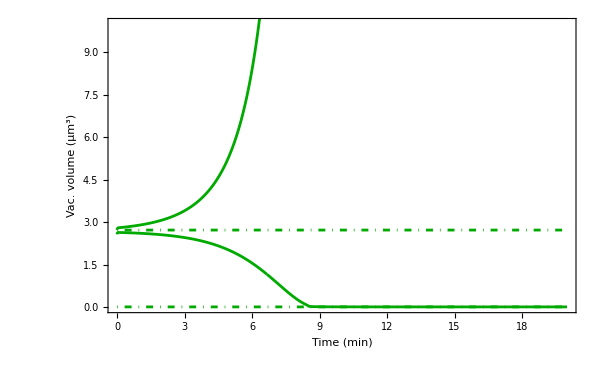

```mathematica
(*--- Plots ---*)
(*--- B.1 First solution ---*)
rVdat2=Table[{tab2[[n,1]],tab2[[n,2,1]]},{n,1,Length[tab2]}];
rCdat2=Table[{tab2[[n,1]],tab2[[n,2,2]]},{n,1,Length[tab2]}];
PCdat2=Table[{tab2[[n,1]],tab2[[n,2,3]]cf},{n,1,Length[tab2]}];
ΓVdat2=Table[{tab2[[n,1]],tab2[[n,2,4]]},{n,1,Length[tab2]}];
ΓCdat2=Table[{tab2[[n,1]],tab2[[n,2,5]]},{n,1,Length[tab2]}];
ϕdat2=Table[{tab2[[n,1]],tab2[[n,2,6]]},{n,1,Length[tab2]}];

ΑVdat2=Table[{tab2[[n,1]],Av[rVdat2[[n,2]],ϕdat2[[n,2]]]},{n,1,Length[tab2]}];
Α1dat2=Table[If[ΑVdat2[[n,2]]≤sC,{ΑVdat2[[n,1]],vacV[rVdat2[[n,2]],ϕdat2[[n,2]]]}],{n,1,Length[tab2]}];
Α1dat2=Select[Α1dat2,Length[#]==2&];
Α2dat2=Table[If[ΑVdat2[[n,2]]>sC,{ΑVdat2[[n,1]],vacV[rVdat2[[n,2]],ϕdat2[[n,2]]]}],{n,1,Length[tab2]}];
Α2dat2=Select[Α2dat2,Length[#]==2&];

(*--- B.2 Second solution ---*)
rVdat3=Table[{tab4[[n,1]],tab4[[n,2,1]]},{n,1,Length[tab4]}];
rCdat3=Table[{tab4[[n,1]],tab4[[n,2,2]]},{n,1,Length[tab4]}];
PCdat3=Table[{tab4[[n,1]],tab4[[n,2,3]]cf},{n,1,Length[tab4]}];
ΓVdat3=Table[{tab4[[n,1]],tab4[[n,2,4]]},{n,1,Length[tab4]}];
ΓCdat3=Table[{tab4[[n,1]],tab4[[n,2,5]]},{n,1,Length[tab4]}];
ϕdat3=Table[{tab4[[n,1]],tab4[[n,2,6]]},{n,1,Length[tab4]}];

ΑVdat3=Table[{tab4[[n,1]],Av[rVdat3[[n,2]],ϕdat3[[n,2]]]},{n,1,Length[tab4]}];
Α1dat3=Table[If[ΑVdat3[[n,2]]≤sC,{ΑVdat2[[n,1]],vacV[rVdat3[[n,2]],ϕdat3[[n,2]]]}],{n,1,Length[tab4]}];
Α1dat3=Select[Α1dat3,Length[#]==2&];
Α2dat3=Table[If[ΑVdat3[[n,2]]>sC,{ΑVdat2[[n,1]],vacV[rVdat3[[n,2]],ϕdat3[[n,2]]]}],{n,1,Length[tab4]}];


f21=Show[
Plot[vacV[eqsol3[[1,1]],eqsol3[[1,6]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[vacV[eqsol3[[2,1]],eqsol3[[2,6]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[vacV[eqsol3[[3,1]],eqsol3[[3,6]]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
(*Plot[π rm^2,{x,t1,t2},PlotStyle->{cdefault,Dashed}],*)
ListPlot[Α1dat2,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat2,Joined->True,PlotStyle->mdefault],
ListPlot[Α1dat3,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat3,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},All},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vac. volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name21=StringJoin["volumeV_",ToString[indx],".pdf"];
Export[name21,f21];

f22=Show[
Plot[vacV[eqsol3[[1,1]],eqsol3[[1,6]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[vacV[eqsol3[[2,1]],eqsol3[[2,6]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[vacV[eqsol3[[3,1]],eqsol3[[3,6]]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
(*Plot[π rm^2,{x,t1,t2},PlotStyle->{cdefault,Dashed}],*)
ListPlot[Α1dat2,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat2,Joined->True,PlotStyle->mdefault],
ListPlot[Α1dat3,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat3,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},{0,10}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vac. volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name22=StringJoin["volumeV_",ToString[indx],"_zoom.pdf"];
Export[name22,f22];
```

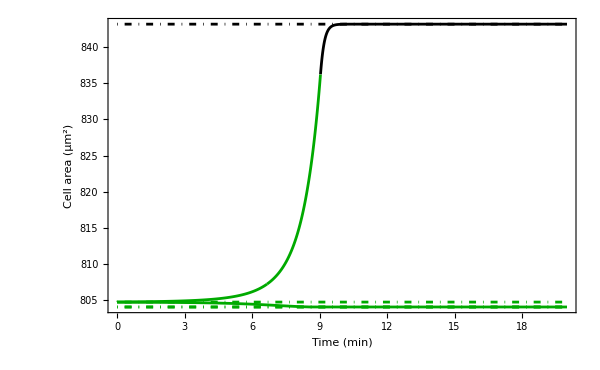

```mathematica
(*--- A.1 Cell area ---*)
(*--- 1st solution ---*)
ΑCdat2=Table[{tab2[[n,1]],4π (rCdat2[[n,2]])^2-π rm^2},{n,1,Length[tab2]}];
Α3dat2=Table[If[ΑCdat2[[n,2]]≤ΑC,ΑCdat2[[n]]],{n,1,Length[tab2]}];
Α3dat2=Select[Α3dat2,Length[#]==2&];
Α4dat2=Table[If[ΑCdat2[[n,2]]>ΑC,ΑCdat2[[n]]],{n,1,Length[tab2]}];
Α4dat2=Select[Α4dat2,Length[#]==2&];
(*--- 2nd solution ---*)
ΑCdat3=Table[{tab4[[n,1]],4π (rCdat3[[n,2]])^2-π rm^2},{n,1,Length[tab4]}];
Α3dat3=Table[If[ΑCdat3[[n,2]]≤ΑC,ΑCdat3[[n]]],{n,1,Length[tab4]}];
Α3dat3=Select[Α3dat3,Length[#]==2&];
Α4dat3=Table[If[ΑCdat3[[n,2]]>ΑC,ΑCdat3[[n]]],{n,1,Length[tab4]}];
Α4dat3=Select[Α4dat3,Length[#]==2&];

f11=Show[Plot[4π (eqsol3[[2,2]])^2-π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[4π (eqsol3[[3,2]])^2-π rm^2,{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[4π (eqsol3[[1,2]])^2-π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[4π R0^2-π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α3dat2,Joined->True,PlotStyle->cdefault],
ListPlot[Α4dat2,Joined->True,PlotStyle->mdefault],
ListPlot[Α4dat3,Joined->True,PlotStyle->mdefault],
ListPlot[Α3dat3,Joined->True,PlotStyle->cdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},{4π R0^2-π rm^2,Max[Α4dat3[[;;,2]]]}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Cell area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name11=StringJoin["cellA_",ToString[indx],".pdf"];
Export[name11,f11];
```

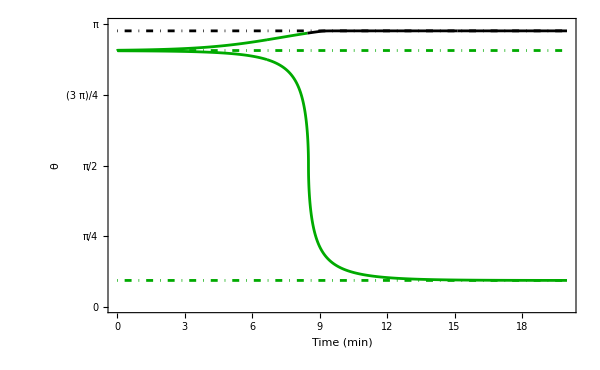

```mathematica
(*--- B.2 Vacuole geometry ---*)
ϕ1dat2=Table[If[ΑVdat2[[n,2]]≤sC,ϕdat2[[n]]],{n,1,Length[tab2]}];
ϕ1dat2=Select[ϕ1dat2,Length[#]==2&];
ϕ2dat2=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ϕdat2,ϕ1dat2];

ϕ1dat3=Table[If[ΑVdat3[[n,2]]≤sC,ϕdat3[[n]]],{n,1,Length[tab4]}];
ϕ1dat3=Select[ϕ1dat3,Length[#]==2&];
ϕ2dat3=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ϕdat3,ϕ1dat3];

f22=Show[
Plot[eqsol3[[1,6]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol3[[2,6]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol3[[3,6]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
ListPlot[ϕ1dat2,Joined->True,PlotStyle->cdefault],
ListPlot[ϕ2dat2,Joined->True,PlotStyle->mdefault],
ListPlot[ϕ1dat3,Joined->True,PlotStyle->cdefault],
ListPlot[ϕ2dat3,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},{0,Pi}},Frame->True,BaseStyle->bfont,
FrameTicks->{{{0,π/4,π/2,3π/4,π},{0,π/4,π/2,3π/4,π}},{Automatic,Automatic}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}},
FrameLabel->{Style["Time (min)",bfont],Style["θ",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name22=StringJoin["phi_",ToString[indx],".pdf"];
Export[name22,f22];
```

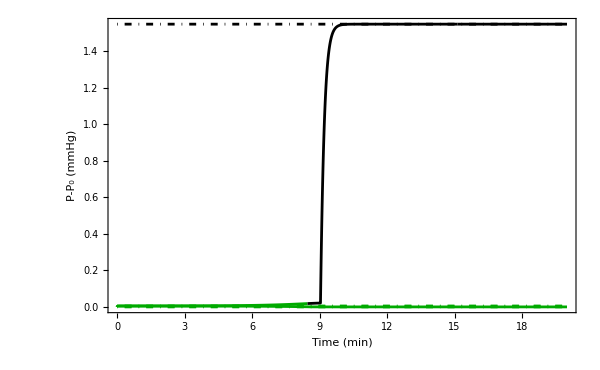

```mathematica
(*--- B.3 Intracellular pressure ---*)
PC1dat2=Table[If[ΑVdat2[[n,2]]≤sC,{PCdat2[[n,1]],PCdat2[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab2]}];
PC1dat2=Select[PC1dat2,Length[#]==2&];
PC2dat2=Table[If[ΑVdat2[[n,2]]>sC,{PCdat2[[n,1]],PCdat2[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab2]}];
PC2dat2=Select[PC2dat2,Length[#]==2&];

PC1dat3=Table[If[ΑVdat3[[n,2]]≤sC,{PCdat3[[n,1]],PCdat3[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab4]}];
PC1dat3=Select[PC1dat3,Length[#]==2&];
PC2dat3=Table[If[ΑVdat3[[n,2]]>sC,{PCdat3[[n,1]],PCdat3[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab4]}];
PC2dat3=Select[PC2dat3,Length[#]==2&];

f23=Show[
Plot[eqsol3[[1,3]]cf-(2(γM+ΤC)/R0) cf,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol3[[2,3]]cf-(2(γM+ΤC)/R0) cf,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol3[[3,3]]cf-(2(γM+ΤC)/R0) cf,{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
(*Plot[(2(γM+ΤC)/R0) cf,{x,t1,t2},PlotRange->All,PlotStyle->{cdefault,DotDashed}],*)ListPlot[PC1dat2,Joined->True,PlotStyle->cdefault],
ListPlot[PC2dat2,Joined->True,PlotStyle->mdefault],
ListPlot[PC1dat3,Joined->True,PlotStyle->cdefault],
ListPlot[PC2dat3,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},
Frame->True,BaseStyle->bfont,FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["P-P_0 (mmHg)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name23=StringJoin["press_",ToString[indx],".pdf"];
Export[name23,f23];
```

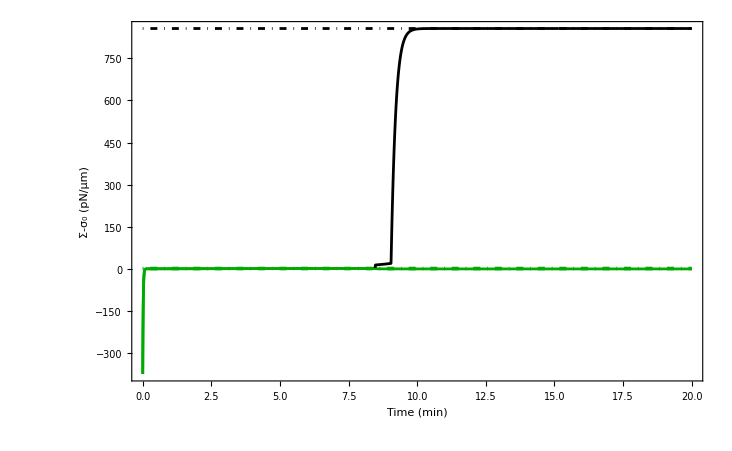

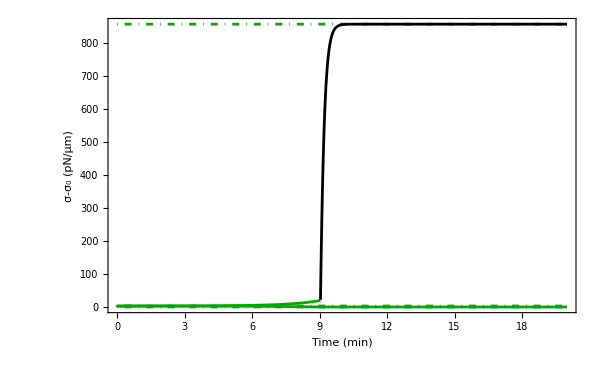

```mathematica
(*--- B.4 Vacuole/cell surface tension ---*)
ΓV1dat2=Table[If[ΑVdat2[[n,2]]≤sC,{ΓVdat2[[n,1]],ΓVdat2[[n,2]]-(γM+ΤC)}],{n,1,Length[tab2]}];
ΓV1dat2=Select[ΓV1dat2,Length[#]==2&];
ΓV2dat2=Table[If[ΑVdat2[[n,2]]>sC,{ΓVdat2[[n,1]],ΓVdat2[[n,2]]-(γM+ΤC)}],{n,1,Length[tab2]}];

ΓV1dat3=Table[If[ΑVdat3[[n,2]]≤sC,{ΓVdat3[[n,1]],ΓVdat3[[n,2]]-(γM+ΤC)}],{n,1,Length[tab4]}];
ΓV1dat3=Select[ΓV1dat3,Length[#]==2&];
ΓV2dat3=Table[If[ΑVdat3[[n,2]]>sC,{ΓVdat3[[n,1]],ΓVdat3[[n,2]]-(γM+ΤC)}],{n,1,Length[tab4]}];

ΓC1dat2=Table[If[ΑCdat2[[n,2]]≤ΑC,{ΓCdat2[[n,1]],ΓCdat2[[n,2]]-(γM+ΤC)}],{n,1,Length[tab2]}];
ΓC1dat2=Select[ΓC1dat2,Length[#]==2&];
ΓC2dat2=Table[If[ΑCdat2[[n,2]]>ΑC,{ΓCdat2[[n,1]],ΓCdat2[[n,2]]-(γM+ΤC)}],{n,1,Length[tab2]}];

ΓC1dat3=Table[If[ΑCdat3[[n,2]]≤ΑC,{ΓCdat3[[n,1]],ΓCdat3[[n,2]]-(γM+ΤC)}],{n,1,Length[tab4]}];
ΓC1dat3=Select[ΓC1dat3,Length[#]==2&];
ΓC2dat3=Table[If[ΑCdat3[[n,2]]>ΑC,{ΓCdat3[[n,1]],ΓCdat3[[n,2]]-(γM+ΤC)}],{n,1,Length[tab4]}];

f24=Show[
Plot[eqsol3[[3,4]]-(γM+ΤC),{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[eqsol3[[2,4]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol3[[1,4]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
(*Plot[γM+ΤC,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],*)
ListPlot[ΓV1dat2,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓV2dat2,Joined->True,PlotStyle->{mdefault,Dashed}],
ListPlot[ΓV1dat3,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓV2dat3,Joined->True,PlotStyle->{mdefault,Dashed}],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name24=StringJoin["tensionV_",ToString[indx],".pdf"];
Export[name24,f24];

f24=Show[
Plot[eqsol3[[1,5]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol3[[2,5]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol3[[3,5]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
(*Plot[eqsol3[[2,5]]-(γM+ΤC),{x,t1,t2},PlotStyle->{cdefault,DotDashed}],*)
(*Plot[γM+ΤC,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],*)
ListPlot[ΓC1dat2,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓC2dat2,Joined->True,PlotStyle->{mdefault,Dashed}],
ListPlot[ΓC1dat3,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓC2dat3,Joined->True,PlotStyle->{mdefault,Dashed}],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name24=StringJoin["tensionC_",ToString[indx],".pdf"];
Export[name24,f24];
```

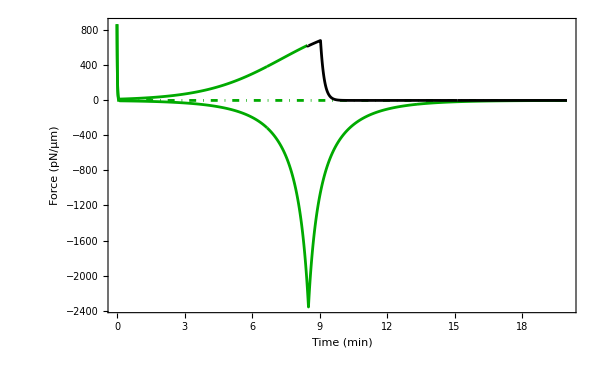

```mathematica
(*--- B.5 Force exerted on vacuole ---*)
F21=Table[If[ΑVdat2[[n,2]]≤sC,F2[[n]]],{n,1,Length[tab2]}];
F21=Select[F21,Length[#]==2&];
F22=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[F2,F21];

F31=Table[If[ΑVdat3[[n,2]]≤sC,F4[[n]]],{n,1,Length[tab4]}];
F31=Select[F31,Length[#]==2&];
F32=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[F4,F31];

f25=Show[Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[F21,Joined->True,PlotStyle->cdefault],
ListPlot[F22,Joined->True,PlotStyle->mdefault],
ListPlot[F31,Joined->True,PlotStyle->cdefault],
ListPlot[F32,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicksStyle->{Directive[bfont,FontFamily->"Arial"],bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Force (pN/μm)",bfont]},FrameStyle->{{bfont,rfont},{bfont,bfont}},ImageSize->imgSize,ImagePadding->imagePadding]
name25=StringJoin["force_",ToString[indx],".pdf"];
Export[name25,f25];
```

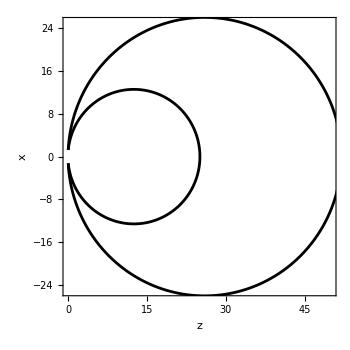

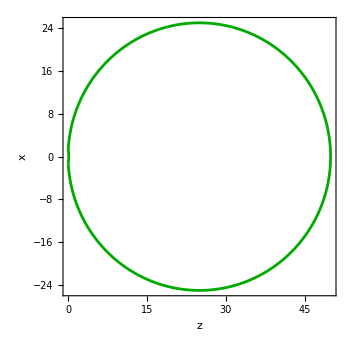

$Aborted

$Aborted

```mathematica
(*--- Animations ---*)
Size=20;imgSize=350;imagePadding={{70,20},{60,2}};
(*--- Auxiliary functions ---*)
Clear[x,y,z];
x[r_,ψ_,ϕ_,f_]:=Module[{},Return[r Cos[ψ]Sin[θ[r ,f]-ϕ]];]
y[r_,ψ_,ϕ_,f_]:=Module[{},Return[r Sin[ψ]Sin[θ[r ,f]-ϕ]];]
z[r_,ϕ_,f_]:=Module[{},Return[r Cos[θ[r,f]-ϕ]-r Cos[θ[r ,f]]];]

(*--- Generate 2D frames ---*)
(*--- 1 frame ---*)
Frame2D[rVdat_,rCdat_,ϕdat_,flag_,l1_,l2_]:=Module[{fig,n,style},n=Length[ρ];
(*--- Choose color ---*)
If[Av[rVdat[[n,2]],ϕdat[[n,2]]]+4π (rCdat[[n,2]])^2-π rm^2≤ΑC,style=cdefault,style=mdefault];
(*--- Generate frame ---*)
fig=Show[ParametricPlot[{z[rVdat[[n,2]],s,flag[[n,2]]],x[rVdat[[n,2]],0,s,flag[[n,2]]]},{s,0,2ϕdat[[n,2]]},PlotStyle->style],
ParametricPlot[{z[rCdat[[n,2]],s,1],x[rCdat[[n,2]],0,s,1]},{s,0,2(π-ArcSin[rVdat[[n,2]]/rCdat[[n,2]] Sin[ϕdat[[n,2]]]])},PlotStyle->style],
Frame->True, FrameTicksStyle->{{bfont,Directive[FontOpacity->0,FontSize->0]},{bfont,Directive[FontOpacity->0,FontSize->0]}},FrameLabel->{Style["z",bfont],Style["x",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding,PlotRange->{l1,l2}];
Return[fig];
]
(*--- Table of frames ---*)
Frame2DEngine[rVdat_,rCdat_,ϕdat_,flag_,tI_,tF_,tS_,l1_,l2_]:=Module[{tab,style,i,f},
i=Position[ρ,SelectFirst[ρ,#1≥tI &]][[1,1]];
f=Position[ρ,SelectFirst[ρ,#1>tF &]]; If[Length[f]==0,f=Length[ρ],f=f[[1,1]]]; 
(*--- Frame engine ---*)
tab=ParallelTable[
(*--- Choose color ---*)
If[Av[rVdat[[n,2]],ϕdat[[n,2]]]+4π (rCdat[[n,2]])^2-π rm^2≤ΑC,style=cdefault,style=mdefault];
(*--- Generate frame ---*)
Show[ParametricPlot[{z[rVdat[[n,2]],s,flag[[n,2]]],x[rVdat[[n,2]],0,s,flag[[n,2]]]},{s,0,2ϕdat[[n,2]]},PlotStyle->style],
ParametricPlot[{z[rCdat[[n,2]],s,1],x[rCdat[[n,2]],0,s,1]},{s,0,2(π-ArcSin[rVdat[[n,2]]/rCdat[[n,2]] Sin[ϕdat[[n,2]]]])},PlotStyle->style],
Frame->True, FrameTicksStyle->{{bfont,Directive[FontOpacity->0,FontSize->0]},{bfont,Directive[FontOpacity->0,FontSize->0]}},FrameLabel->{Style["z",bfont],Style["x",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding,PlotRange->{l1,l2}],{n,i,f,tS}];
Return[tab];
]

(*--- Plot 2D ---*)
(*--- Exemplary frame ---*)
fig1=Frame2D[rVdat1,rCdat1,ϕdat1,flag1,{0,50},{-25,25}]
fig2=Frame2D[rVdat4,rCdat4,ϕdat4,flag4,{0,50},{-25,25}]
frames2D1=Frame2DEngine[rVdat1,rCdat1,ϕdat1,flag1,0 60,5 60,5,{0,50},{-25,25}];
frames2D2=Frame2DEngine[rVdat4,rCdat4,ϕdat4,flag4,15 60,25 60,10,{0,50},{-25,25}];
```

```mathematica
(*--- Animation ---*)
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/dynamics/",date]];
If[DirectoryQ["movies"]==False,CreateDirectory["movies"]];SetDirectory["movies"];
(*--- Movie 1 ---*)
If[DirectoryQ["movie2D_1"]==False,CreateDirectory["movie2D_1"]]; SetDirectory["movie2D_1"];
movie2D1=ListAnimate[frames2D1,AnimationRepetitions->1];
Export["frame001.png",frames2D1,"VideoFrames"];
(*--- Movie 2 ---*)
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/dynamics/",date,"/movies"]];If[DirectoryQ["movie2D_2"]==False,CreateDirectory["movie2D_2"]]; SetDirectory["movie2D_2"];
movie2D2=ListAnimate[frames2D2,AnimationRepetitions->1];
Export["frame001.png",frames2D2,"VideoFrames"];
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/dynamics/",date]];
```

```mathematica
(*--- Plot 3D ---*)
(*--- Generate frames ---*)
(*--- 1 frame ---*)
Frame3D[rVdat_,rCdat_,ϕdat_,flag_,l1_,l2_,l3_]:=Module[{fig,n,style},n=Length[ρ];
(*--- Choose color ---*)
If[Av[rVdat[[n,2]],ϕdat[[n,2]]]+4π (rCdat[[n,2]])^2-π rm^2≤ΑC,style=cdefault,style=Directive[Gray,AbsoluteThickness[2]]];
(*--- Generate frame ---*)
fig=Show[ParametricPlot3D[{x[rVdat[[n,2]],ϕ,s,flag[[n,2]]],y[rVdat[[n,2]],ϕ,s,flag[[n,2]]],z[rVdat[[n,2]],s,flag[[n,2]]]},{ϕ,-π/8,3π/2},{s,0,ϕdat[[n,2]]},PlotStyle->style,Mesh->None],
ParametricPlot3D[{x[rCdat[[n,2]],ϕ,s,1],y[rCdat[[n,2]],ϕ,s,1],z[rCdat[[n,2]],s,1]},{ϕ,-π/8,3π/2},{s,0,π-ArcSin[rVdat[[n,2]]/rCdat[[n,2]] Sin[ϕdat[[n,2]]]]},PlotStyle->style,Mesh->None],
PlotRange->{l1,l2,l3},AxesLabel->{"x","y","z"},LabelStyle->{bfont},Frame->True,PlotRangeClipping->False];
Return[fig];
]
(*--- Table of frames ---*)
Frame3DEngine[rVdat_,rCdat_,ϕdat_,flag_,tI_,tF_,tS_,l1_,l2_,l3_]:=Module[{tab,i,f,style},
i=Position[ρ,SelectFirst[ρ,#1≥tI &]][[1,1]];
f=Position[ρ,SelectFirst[ρ,#1>tF &]]; If[Length[f]==0,f=Length[ρ],f=f[[1,1]]]; 
tab=ParallelTable[
(*--- Choose color ---*)
If[Av[rVdat[[n,2]],ϕdat[[n,2]]]+4π (rCdat[[n,2]])^2-π rm^2≤ΑC,style=cdefault,style=Directive[Gray,AbsoluteThickness[2]]];
(*--- Generate frame ---*)
Show[
ParametricPlot3D[{x[rVdat[[n,2]],ϕ,s,flag[[n,2]]],y[rVdat[[n,2]],ϕ,s,flag[[n,2]]],z[rVdat[[n,2]],s,flag[[n,2]]]},{ϕ,-π/8,3π/2},{s,0,ϕdat[[n,2]]},PlotStyle->style,Mesh->None],
ParametricPlot3D[{x[rCdat[[n,2]],ϕ,s,1],y[rCdat[[n,2]],ϕ,s,1],z[rCdat[[n,2]],s,1]},{ϕ,-π/8,3π/2},{s,0,π-ArcSin[rVdat[[n,2]]/rCdat[[n,2]] Sin[ϕdat[[n,2]]]]},PlotStyle->style,Mesh->None],
PlotRange->{l1,l2,l3},AxesLabel->{"x","y","z"},LabelStyle->{bfont},Frame->True,PlotRangeClipping->False],{n,i,f,tS}];
Return[tab];
]

(*--- Exemplary frame ---*)
fig1=Frame3D[rVdat1,rCdat1,ϕdat1,flag1,{-25,25},{-25,25},{0,55}]
fig2=Frame3D[rVdat4,rCdat4,ϕdat4,flag4,{-25,25},{-25,25},{0,55}]
frames3D1=Frame3DEngine[rVdat1,rCdat1,ϕdat1,flag1,0 60,5 60,5,{-25,25},{-25,25},{0,55}];
frames3D2=Frame3DEngine[rVdat4,rCdat4,ϕdat4,flag4,15 60,25 60,10,{-25,25},{-25,25},{0,55}];
```

-Graphics3D-

-Graphics3D-

```mathematica
(*--- Animation ---*)
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/dynamics/",date]];
If[DirectoryQ["movies"]==False,CreateDirectory["movies"]];SetDirectory["movies"];
(*--- Movie 1 ---*)
If[DirectoryQ["movie3D_1"]==False,CreateDirectory["movie3D_1"]]; SetDirectory["movie3D_1"];
movie3D1=ListAnimate[frames3D1,AnimationRepetitions->1];
Export["frame001.png",frames3D1,"VideoFrames"];
(*--- Movie 2 ---*)
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/dynamics/",date,"/movies"]];If[DirectoryQ["movie3D_2"]==False,CreateDirectory["movie3D_2"]]; SetDirectory["movie3D_2"];
movie3D2=ListAnimate[frames3D2,AnimationRepetitions->1];
Export["frame001.png",frames3D2,"VideoFrames"];
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/dynamics/",date]];
```

```mathematica
(*f14=Show[Plot[eqsol1[[2,4]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[γM+ΤC,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓV1dat1,Joined->True,PlotStyle->{cdefault}],
(*ListPlot[ΓC1dat1,Joined->True,PlotStyle->cdefault],*)
ListPlot[ΓV2dat1,Joined->True,PlotStyle->{mdefault,Dashed}],
ListPlot[ΓC2dat1,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{{All,All},{Automatic,Automatic}},FrameTicksStyle->{{bfont,Directive[Darker[Red],FontOpacity->1,FontSize->Size,FontFamily->"Arial"]},{bfont,Directive[FontOpacity->0,FontSize->0,FontFamily->"Arial"]}},
FrameLabel->{{Style["σ (pN/μm)",bfont],Style["Σ (pN/μm)",rfont]},{Style["Time (min)",bfont],None}},FrameStyle->{{bfont,rfont},{bfont,bfont}},ImageSize->imgSize,ImagePadding->imagePadding]
name14=StringJoin["s1_",ToString[date],".pdf"];
Export[name14,f14];*)
```

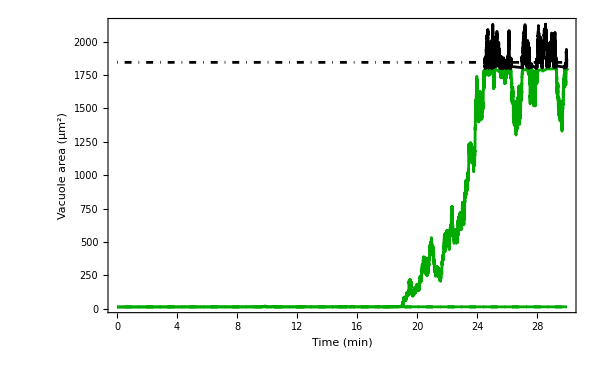

```mathematica
(*(*--- B.6 Effects of large fluctuations: radius ---*)
indx=4;
Α1dat4=Table[If[ΑCdat4[[n,2]]+ΑVdat4[[n,2]]-π rm^2≤ΑC,ΑVdat4[[n]]],{n,1,Length[tab4]}];
Α1dat4=Select[Α1dat4,Length[#]==2&];
Α2dat4=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΑVdat4,Α1dat4];

t2=30;
f26=Show[Plot[Av[eqsol2[[1,1]],eqsol2[[1,5]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[Av[eqsol2[[3,1]],eqsol2[[3,5]]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α1dat2,Joined->True,PlotStyle->cdefault],
ListPlot[Α1dat4,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat2,Joined->True,PlotStyle->mdefault],
ListPlot[Α2dat4,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},All},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vacuole area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name26=StringJoin["areaV_",ToString[indx],".pdf"];
Export[name26,f26];*)
```

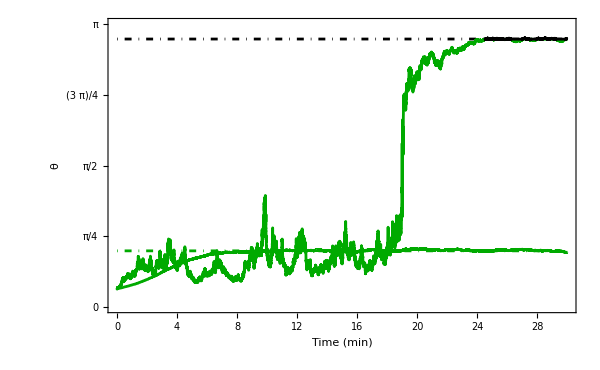

```mathematica
(*(*--- B.7 Effects of large fluctuations: Vacuole geometry ---*)
ϕ1dat4=Table[If[ΑCdat4[[n,2]]+ΑVdat4[[n,2]]-π rm^2≤ΑC,ϕdat4[[n]]],{n,1,Length[tab4]}];
ϕ1dat4=Select[ϕ1dat4,Length[#]==2&];
ϕ2dat4=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ϕdat4,ϕ1dat4];

f27=Show[Plot[eqsol2[[1,5]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol2[[3,5]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
ListPlot[ϕ1dat2,Joined->True,PlotStyle->cdefault],
ListPlot[ϕ1dat4,Joined->True,PlotStyle->cdefault],
ListPlot[ϕ2dat2,Joined->True,PlotStyle->mdefault],
ListPlot[ϕ2dat4,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},{0,Pi}},Frame->True,BaseStyle->bfont,
FrameTicks->{{{0,π/4,π/2,3π/4,π},{0,π/4,π/2,3π/4,π}},{Automatic,Automatic}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}},
FrameLabel->{Style["Time (min)",bfont],Style["θ",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name27=StringJoin["phi_",ToString[indx],".pdf"];
Export[name27,f27];*)
```

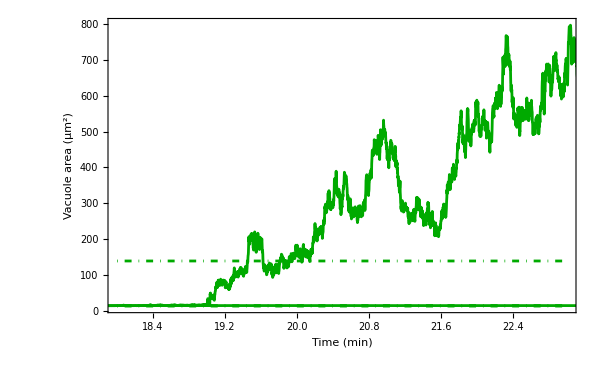

```mathematica
(*(*--- B.8 Effects of large fluctuations: zoom ---*)
t1=18;t2=23;
f28=Show[Plot[Av[eqsol2[[1,1]],eqsol2[[1,5]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[Av[eqsol2[[2,1]],eqsol2[[2,5]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α1dat2,Joined->True,PlotStyle->cdefault],
ListPlot[Α1dat4,Joined->True,PlotStyle->cdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},{10,800}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vacuole area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name28=StringJoin["areaVzoom_",ToString[indx],".pdf"];
Export[name28,f28];*)
```

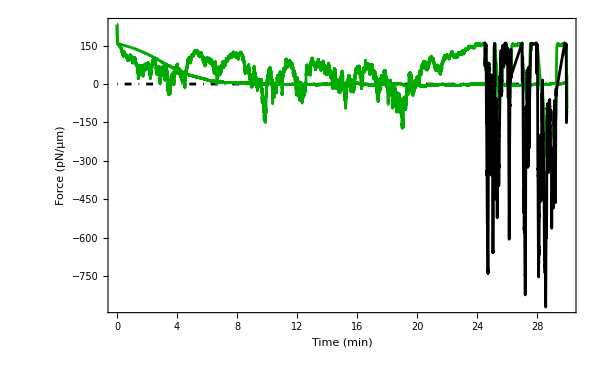

```mathematica
(*(*--- B.9 Effects of large fluctuations: force ---*)
t1=0;t2=30;
F41=Table[If[ΑCdat4[[n,2]]+ΑVdat4[[n,2]]-π rm^2≤ΑC,F4[[n]]],{n,1,Length[tab4]}];
F41=Select[F41,Length[#]==2&];
F42=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[F4,F41];

f29=Show[Plot[0,{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
ListPlot[F21,Joined->True,PlotStyle->cdefault],
ListPlot[F41,Joined->True,PlotStyle->cdefault],
ListPlot[F22,Joined->True,PlotStyle->mdefault],
ListPlot[F42,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicksStyle->{Directive[bfont,FontFamily->"Arial"],bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Force (pN/μm)",bfont]},FrameStyle->{{bfont,rfont},{bfont,bfont}},ImageSize->imgSize,ImagePadding->imagePadding]
name29=StringJoin["force_",ToString[indx],".pdf"];
Export[name29,f29];*)
```

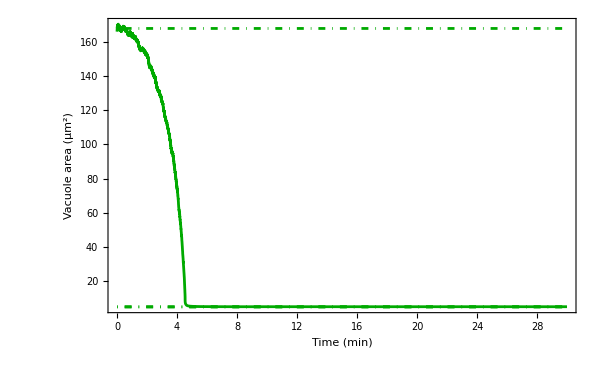

```mathematica
(*(*--- C. Mixed phase: Initial condition 2 ---*)
rVdat3=Table[{tab3[[n,1]],tab3[[n,2,1]]},{n,1,Length[tab3]}];
rCdat3=Table[{tab3[[n,1]],tab3[[n,2,2]]},{n,1,Length[tab3]}];
PCdat3=Table[{tab3[[n,1]],tab3[[n,2,3]]cf},{n,1,Length[tab3]}];
ΓVdat3=Table[{tab3[[n,1]],tab3[[n,2,4]]},{n,1,Length[tab3]}];
ΓCdat3=Table[{tab3[[n,1]],tab3[[n,2,5]]},{n,1,Length[tab3]}];
ϕdat3=Table[{tab3[[n,1]],tab3[[n,2,6]]},{n,1,Length[tab3]}];

ΑVdat3=Table[{tab3[[n,1]],Av[rVdat3[[n,2]],ϕdat3[[n,2]]]},{n,1,Length[tab3]}];
ΑCdat3=Table[{tab3[[n,1]],4π (rCdat3[[n,2]])^2},{n,1,Length[tab3]}];
t1=0;t2=30; indx=3;

(*--- C.1 Vacuole area ---*)
Α1dat3=Table[If[ΑCdat3[[n,2]]+ΑVdat3[[n,2]]-π rm^2≤ΑC,ΑVdat3[[n]]],{n,1,Length[tab3]}];
Α1dat3=Select[Α1dat3,Length[#]==2&];
Α2dat3=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΑVdat3,Α1dat3];

f31=Show[Plot[Av[eqsol2[[1,1]],eqsol2[[1,5]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[Av[eqsol2[[2,1]],eqsol2[[2,5]]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],Plot[π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α1dat3,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat3,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},All},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vacuole area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name31=StringJoin["areaV_",ToString[indx],".pdf"];
Export[name31,f31];*)
```

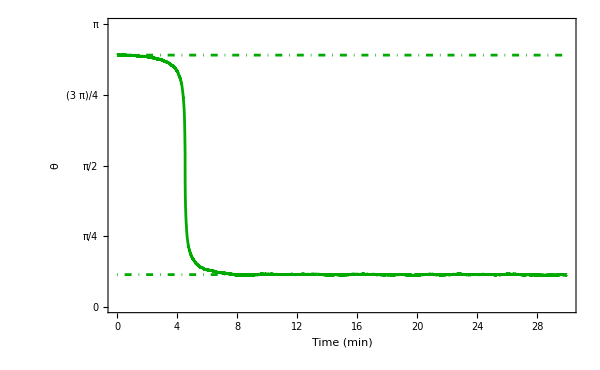

```mathematica
(*(*--- C.2 Vacuole geometry ---*)
ϕ1dat3=Table[If[ΑCdat3[[n,2]]+ΑVdat3[[n,2]]-π rm^2≤ΑC,ϕdat3[[n]]],{n,1,Length[tab3]}];
ϕ1dat3=Select[ϕ1dat3,Length[#]==2&];
ϕ2dat3=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ϕdat3,ϕ1dat3];

f32=Show[Plot[eqsol2[[2,5]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol2[[1,5]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ϕ1dat3,Joined->True,PlotStyle->cdefault],
ListPlot[ϕ2dat3,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},{0,Pi}},Frame->True,BaseStyle->bfont,
FrameTicks->{{{0,π/4,π/2,3π/4,π},{0,π/4,π/2,3π/4,π}},{Automatic,Automatic}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}},
FrameLabel->{Style["Time (min)",bfont],Style["θ",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name32=StringJoin["phi_",ToString[indx],".pdf"];
Export[name32,f32];*)
```

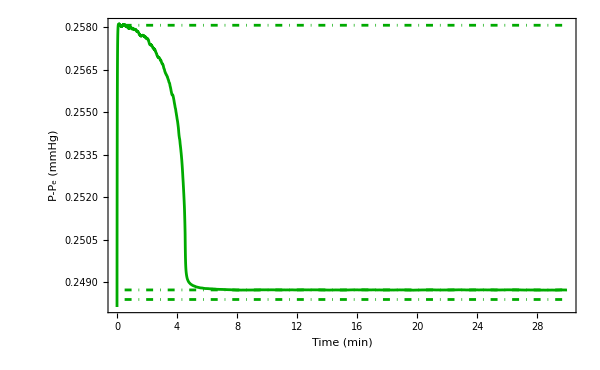

```mathematica
(*(*--- C.3 Intracellular pressure ---*)
PC1dat3=Table[If[ΑCdat3[[n,2]]+ΑVdat3[[n,2]]-π rm^2≤ΑC,PCdat3[[n]]],{n,1,Length[tab3]}];
PC1dat3=Select[PC1dat3,Length[#]==2&];
PC2dat3=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[PCdat3,PC1dat3];

f33=Show[Plot[eqsol2[[1,3]]cf,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol2[[2,3]]cf,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[(2(γM+ΤC)/R0) cf,{x,t1,t2},PlotRange->All,PlotStyle->{cdefault,DotDashed}],ListPlot[PC1dat3,Joined->True,PlotStyle->cdefault],
ListPlot[PC2dat3,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},
Frame->True,BaseStyle->bfont,FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["P-P_e (mmHg)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name33=StringJoin["press_",ToString[indx],".pdf"];
Export[name33,f33];*)
```

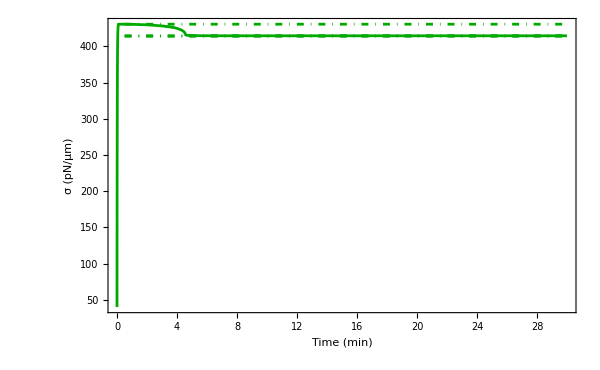

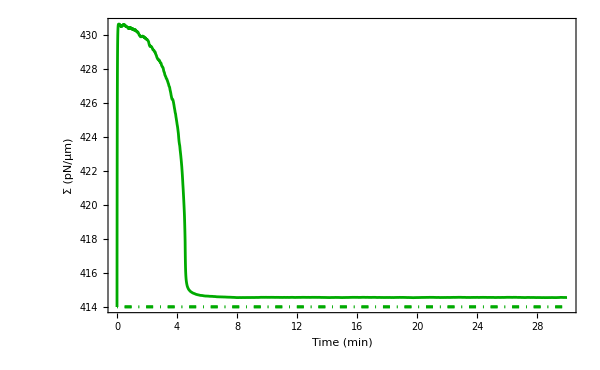

```mathematica
(*(*--- C.4 Vacuole/cell surface tension ---*)
ΓV1dat3=Table[If[ΑCdat3[[n,2]]+ΑVdat3[[n,2]]-π rm^2≤ΑC,ΓVdat3[[n]]],{n,1,Length[tab3]}];
ΓV1dat3=Select[ΓV1dat3,Length[#]==2&];
ΓV2dat3=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΓVdat3,ΓV1dat3];

ΓC1dat3=Table[If[ΑCdat3[[n,2]]+ΑVdat3[[n,2]]-π rm^2≤ΑC,ΓCdat3[[n]]],{n,1,Length[tab3]}];
ΓC1dat3=Select[ΓC1dat3,Length[#]==2&];
ΓC2dat3=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΓCdat3,ΓC1dat3];

f34=Show[Plot[eqsol2[[1,4]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[eqsol2[[2,4]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[γM+ΤC,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓV1dat3,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓV2dat3,Joined->True,PlotStyle->{mdefault,Dashed}],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["σ (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name34=StringJoin["tensionV_",ToString[indx],".pdf"];
Export[name34,f34];

f34=Show[Plot[eqsol3[[1,4]],{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Plot[γM+ΤC,{q,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓC1dat3,Joined->True,PlotStyle->{cdefault}],
ListPlot[ΓC2dat3,Joined->True,PlotStyle->{mdefault,Dashed}],PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{{All,None},{Automatic,None}},FrameTicksStyle->{bfont,bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Σ (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name34=StringJoin["tensionC_",ToString[indx],".pdf"];
Export[name34,f34];*)
```

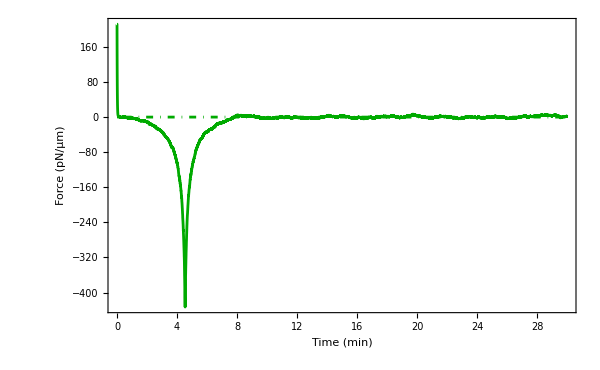

```mathematica
(*(*--- C.5 Force exerted on vacuole ---*)
F31=Table[If[ΑCdat3[[n,2]]+ΑVdat3[[n,2]]-π rm^2≤ΑC,F3[[n]]],{n,1,Length[tab3]}];
F31=Select[F31,Length[#]==2&];
F32=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[F3,F31];

f35=Show[Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],ListPlot[F31,Joined->True,PlotStyle->cdefault],
ListPlot[F32,Joined->True,PlotStyle->mdefault],
PlotRange->{{t1,t2},All},Frame->True,BaseStyle->bfont,
FrameTicksStyle->{Directive[bfont,FontFamily->"Arial"],bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Force (pN/μm)",bfont]},FrameStyle->{{bfont,rfont},{bfont,bfont}},ImageSize->imgSize,ImagePadding->imagePadding]
name35=StringJoin["force_",ToString[indx],".pdf"];
Export[name35,f35];*)
```

```mathematica
(*EqsSet[p_,t0_,rV0_,rC0_,a_,ΓV0_,ΓC0_]:={
(*--- Initial conditions ---*)
r[t0]==rV0,σ[t0]==ΓC0,Σ[t0]==ΓV0,Φ[t0]==ΓC0,
(*--- Surface tensions ---*)
(*--- eq. 1: Cell ---*)
σ'[t]==1/λ[t](σL[t]-σ[t]),
(*--- eq. 2: Inverse bleb ---*)
(*--- cortex-dominated regime: pure growth term ---*)
(*--- membrane-dominated regime: lipid flow Φ ---*)
Σ'[t]==1/ξ[t](Φ[t]-Σ[t]),
(*--- eq. 3: Inverse bleb radius ---*)
F[t]==(-p+(2σ[t])/R[t]+(2Σ[t])/r[t])((1-ζ[t])/2)+(p-(2σ[t])/R[t]-(2Σ[t])/r[t])((1+ζ[t])/2),
r'[t]==r[t]/(4ν0)F[t],
(*--- other specs: additional functions ---*)
(*--- eq 4: Cell radius ---*)
R[t]==((rC0)^3+(r[t])^3(2+Cos[θ[t]])(Sin[θ[t]/2])^4)^(1/3),
(*--- eq 5: Inverse bleb opening angle ---*)
θ[t]==(ArcSin[a/r[t]])((1-ζ[t])/2)+(π-ArcSin[a/r[t]])((1+ζ[t])/2),
(*--- eq 6.1: Limit surface tension of the cell ---*)
Α[t]==4π (R[t])^2-π (a)^2,
σL[t]==Re[γM+ΤC+Δσ/ΔΑ(Α[t]/Α0-1)^α]((1-s2[t])/2)+Re[γM+ΤC+Δσ+b( Exp[(Α[t]-ΑC)/ΑC]-1)]((1+s2[t])/2),
(*--- eq 6.2: Limit surface tension of the inverse bleb ---*)
s[t]==2π(r[t])^2(1-Cos[θ[t]]),
(*--- Lipid flow drag ---*)
γ[t]==(2π)/η0 Re[Δσ/Δs α/s0(s[t]/s0-1)^(α-1)]((1-s1[t])/2)+(2π)/η0 b/sC( Exp[(s[t]-sC)/sC])((1+s1[t])/2),
Φ'[t]==γ[t](σ[t]-Σ[t]),
(*--- eq 7: Tensional timescales ---*)
ξ[t]==τ0((1-s1[t])/2)+τM((1+s1[t])/2),
λ[t]==τ0((1-s2[t])/2)+τM((1+s2[t])/2),
(*--- other specs: special events ---*)
(*--- 1. Inverse bleb area expansion ---*)
s1[t0]==-1,
WhenEvent[s[t]-sC>0,s1[t]->"DiscontinuitySignature"],
(*--- 2. Cell area expansion ---*)
s2[t0]==-1,
WhenEvent[Α[t]-ΑC>0,s2[t]->"DiscontinuitySignature"],
(*--- 2. Dealing with behaviour at hemisphere ---*)
ζ[t0]==1,
WhenEvent[r[t]-a<10^-6,ζ[t]->"DiscontinuitySignature",
"DetectionMethod"->"Interpolation","LocationMethod"->"BrentBracketRoot"]
};
*)
```